# PhD Thesis

Title: Quantum Machine Leaning and Information Processing
Author: Pei-Xin Shen
Advisor: Dong-Ling Deng
Affiliation: Institute of Interdisciplinary Information Sciences, Tsinghua University
Date: April 2nd 2022
License: MIT

# Chapter 1 Preliminaries

## Quantum Computation

## Block Sphere

```mathematica
Clear["Global`*"];
vectorBloch[theta_,phi_]:= Graphics3D[
{RGBColor[0.9058823529411765, 0.027450980392156862, 0.12941176470588237],Arrowheads[0.04],Arrow[Tube[{{0,0,0},Dynamic@{Sin[theta] Cos[phi],Sin[theta]Sin[phi],Cos[theta]}},.02]]},Boxed->False,Axes->False,ImageSize->450] (*unit Bloch vector*)
xyz=ParametricPlot3D[{{Cos[t], Sin[t],0},{0, Cos[t], Sin[t]},{ Cos[t],0,Sin[t]}},{t,0,2 π},PlotStyle->{{Black,Thick,Dashed},{Black,Thick,Dashed},{Black,Thick,Dashed}},Boxed->False,Axes->False,ImageSize->400];
poincareBloch[theta_,phi_]:=
Graphics3D[{Opacity[0.1],RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],Sphere[],Black,Thick,Opacity[1],
PointSize[.02],Point[{0,0,0}],Point[{1,0,0}],Point[{-1,0,0}],Point[{0,1,0}],Point[{0,-1,0}],Point[{0,0,1}],Point[{0,0,-1}],
Line[{{0,1,0},{0,-1,0}}],
Line[{{0,0,1},{0,0,-1}}],
Line[{{1,0,0},{-1,0,0}}],
{Dotted,Line[{{Sin[theta] Cos[phi],Sin[theta]Sin[phi],0},{Sin[theta] Cos[phi],Sin[theta]Sin[phi],Cos[theta]}}]},
{Dotted,Line[{{0,0,0},{Sin[theta] Cos[phi],Sin[theta]Sin[phi],0}}]},
{Dashed,RGBColor[0.9058823529411765, 0.027450980392156862, 0.12941176470588237],BezierCurve[{{Sin[theta] Cos[0],Sin[theta]Sin[0],0},{Sin[theta] Cos[phi/2],Sin[theta]Sin[phi/2],0},{Sin[theta] Cos[phi],Sin[theta]Sin[phi],0}}/1.4]},
{Dashed,RGBColor[0.9058823529411765, 0.027450980392156862, 0.12941176470588237],BezierCurve[{{Sin[0] Cos[phi],Sin[0]Sin[phi],Cos[0]},{Sin[theta/2] Cos[phi],Sin[theta/2]Sin[phi],Cos[theta/2]},{Sin[theta] Cos[phi],Sin[theta]Sin[phi],Cos[theta]}}/2.3]},
Text[Style["θ", 14,FontFamily->"Times"], {-0.15,0.7,0}],
Text[Style["ϕ", 14,FontFamily->"Times"], {0.6,0.12,0}],
Text[Style[Row[{"|0⟩=",MatrixForm[{1,0}]}], 14,FontFamily->"Times"], {0,0,1.3 }],
Text[Style[Row[{"|1⟩=",MatrixForm[{0,1}]}], 14,FontFamily->"Times"], {0,0,-1.4 }],
Text[Style[Row[{"1/(√2)",MatrixForm[{1,ⅈ}]}], 14,FontFamily->"Times"], {0,1.6,0}],
Text[Style[Row[{"1/(√2)",MatrixForm[{1,-ⅈ}]}], 14,FontFamily->"Times"],{0,-1.44 ,0}],
Text[Style[Row[{"1/(√2)",MatrixForm[{1,1}]}], 14,FontFamily->"Times"], {1.3 ,-0.25,0}],
Text[Style[Row[{"1/(√2)",MatrixForm[{1,-1}]}],14,FontFamily->"Times"],{-1.5 ,0.3,0}],
Boxed->False,Axes->False,ImageSize->400}]
Show[
poincareBloch[π/4,0.4],
vectorBloch[π/4,0.4],
xyz,
Boxed->False,Axes->True,ImageSize->{400,400},ViewAngle->π/12]
```

-Graphics3D-

## Quantum Circuits

```mathematica
Clear["Global`*"];
<<Wolfram`QuantumFramework`
```

### Quantum teleportation

```mathematica
qc=QuietEcho@QuantumCircuitOperator[{QuantumOperator["H",{2}],QuantumOperator["CX",{2,3}],QuantumOperator["CX"],QuantumOperator["H"],QuantumOperator["CX",{2,3}],QuantumOperator["CZ",{1,3}],QuantumMeasurementOperator[],QuantumMeasurementOperator[{2}]}];
qc["Diagram",ImageSize->600]
```

-Graphics-

## Condensed Matter Theory

## The Bethe Ansatz

### The Exact Solution of Heisenberg Model

```mathematica
Clear["Global`*"];
fixGlobalPhase[waveFunc_]:=waveFunc*Exp[-ⅈ Arg@FirstCase[waveFunc,x_/;Abs[x]>10^-5]]
indexToBasis[index_]:=ReplacePart[Table[0,Nt],Partition[index,1]->1]
basisToIndex[basis_]:=Flatten@Position[basis,1]
mod[k_,N_:Nt]:=Mod[k-1,N]+1

S=1/2;
{Ι,𝕏,𝕐,ℤ}=PauliMatrix@{0,1,2,3};
𝕊=S*{𝕏,𝕐,ℤ};𝕀={Ι,Ι,Ι};
Nt=5;
𝒮[i_]:=MapThread[KroneckerProduct,ReplacePart[Table[𝕀,Nt],{i->𝕊}]]
𝒮[Nt+1]:=𝒮[1]
𝒮p[i_]:=(𝒮[i][[1]]+ⅈ 𝒮[i][[2]])
𝒮m[i_]:=(𝒮[i][[1]]-ⅈ 𝒮[i][[2]])
i_·j_:=Total@MapThread[Dot,{i,j}]

basisCon=Tuples[{0,1},Nt];
basisLen=Length@basisCon;
basisTag=Dispatch@Thread[basisCon->Range@basisLen];
H=-J*Sum[𝒮[i]·𝒮[i+1],{i,Nt}];
E0=-J Nt/4;
{vals,vecs}=SortBy[Eigensystem[H]ᵀ,N[#[[1]]/.J->1]&]ᵀ;
vals
```

{-(5 J)/4,-(5 J)/4,-(5 J)/4,-(5 J)/4,-(5 J)/4,-(5 J)/4,-(√5 J)/4,-(√5 J)/4,-(√5 J)/4,-(√5 J)/4,-(√5 J)/4,-(√5 J)/4,-(√5 J)/4,-(√5 J)/4,1/4 (3-2 √5) J,1/4 (3-2 √5) J,1/4 (3-2 √5) J,1/4 (3-2 √5) J,(√5 J)/4,(√5 J)/4,(√5 J)/4,(√5 J)/4,(√5 J)/4,(√5 J)/4,(√5 J)/4,(√5 J)/4,(3 J)/4,(3 J)/4,1/4 (3+2 √5) J,1/4 (3+2 √5) J,1/4 (3+2 √5) J,1/4 (3+2 √5) J}

### The Reference State

```mathematica
{spinUp,spinDn}={{{1},{0}},{{0},{1}}};
state0th=Flatten@*KroneckerProduct@@Table[spinUp,Nt];
H.state0th==E0 state0th
basisCon[[Flatten@Position[vecs[[1]],x_/;x!=0]]]
```

True

{{1,1,1,1,1}}

### The Subspace of One Magnon

```mathematica
basis1st=Select[Count[#,1]==1&][basisCon];
(*ansatz1st=∑_(n=1)^Nt a[n]𝒮m[n].state0th*)
ansatz1st=Sum[a@@Flatten@Position[conf,1]*UnitVector[2^Nt,conf/.basisTag],{conf,basis1st}];

condiEqs=SortBy[#[[1,1,3]]&]@FullSimplify@Thread[Equal[DeleteCases[H.ansatz1st-Ε ansatz1st,0],0]];
condiMat=Normal@CoefficientArrays[condiEqs,Array[a,Nt]][[2]];
MatrixForm/@{condiEqs,condiMat}
SortBy[SolveValues[Det[condiMat]==0,Ε],#/.J->1&]
```

{(4 Ε a[1]+J (a[1]+2 (a[2]+a[5]))==0
4 Ε a[2]+J (2 a[1]+a[2]+2 a[3])==0
4 Ε a[3]+J (2 a[2]+a[3]+2 a[4])==0
4 Ε a[4]+J (2 a[3]+a[4]+2 a[5])==0
2 J (a[1]+a[4])+(J+4 Ε) a[5]==0),(J+4 Ε | 2 J | 0 | 0 | 2 J
2 J | J+4 Ε | 2 J | 0 | 0
0 | 2 J | J+4 Ε | 2 J | 0
0 | 0 | 2 J | J+4 Ε | 2 J
2 J | 0 | 0 | 2 J | J+4 Ε)}

{-(5 J)/4,-(√5 J)/4,-(√5 J)/4,(√5 J)/4,(√5 J)/4}

```mathematica
effeMat=Ε IdentityMatrix[Nt]-condiMat/4;Simplify@MatrixForm[effeMat]
SortBy[FullSimplify@Table[Block[{k=2π m/Nt},effeMat[[1]].Exp[ⅈ k Range[0,Nt-1]]]//Simplify,{m,0,Nt-1}],#/.J->1&]
SortBy[FullSimplify@Table[J(1-Cos[k])+E0,{k,Table[2π m/Nt,{m,Nt}]}],#/.J->1&]
```

(-J/4 | -J/2 | 0 | 0 | -J/2
-J/2 | -J/4 | -J/2 | 0 | 0
0 | -J/2 | -J/4 | -J/2 | 0
0 | 0 | -J/2 | -J/4 | -J/2
-J/2 | 0 | 0 | -J/2 | -J/4)

{-(5 J)/4,-(√5 J)/4,-(√5 J)/4,(√5 J)/4,(√5 J)/4}

{-(5 J)/4,-(√5 J)/4,-(√5 J)/4,(√5 J)/4,(√5 J)/4}

```mathematica
condiEqs=SortBy[#[[1,1,3]]&]@FullSimplify@Table[(Ε-Ε0) a[x]==-J(-Δ a[x]+1/2(a[x-1]+a[x+1])),{x,Nt}]/.{a[0]->a[Nt],a[Nt+1]->a[1]};
condiMat=Normal@CoefficientArrays[condiEqs,Array[a,Nt]][[2]];
MatrixForm/@{condiEqs,condiMat}
SortBy[SolveValues[Det[condiMat]==0,Ε]/.{Δ->1,Ε0->E0},#/.J->1&]
```

{(2 (Ε-Ε0) a[1]+J (-2 Δ a[1]+a[2]+a[5])==0
2 (Ε-Ε0) a[2]+J (a[1]-2 Δ a[2]+a[3])==0
2 (Ε-Ε0) a[3]+J (a[2]-2 Δ a[3]+a[4])==0
2 (Ε-Ε0) a[4]+J (a[3]-2 Δ a[4]+a[5])==0
2 (Ε-Ε0) a[5]+J (a[1]+a[4]-2 Δ a[5])==0),(-2 J Δ+2 (Ε-Ε0) | J | 0 | 0 | J
J | -2 J Δ+2 (Ε-Ε0) | J | 0 | 0
0 | J | -2 J Δ+2 (Ε-Ε0) | J | 0
0 | 0 | J | -2 J Δ+2 (Ε-Ε0) | J
J | 0 | 0 | J | -2 J Δ+2 (Ε-Ε0))}

{-(5 J)/4,-(√5 J)/4,-(√5 J)/4,(√5 J)/4,(√5 J)/4}

```mathematica
effeMat=Ε IdentityMatrix[Nt]-condiMat/2;Simplify@MatrixForm[effeMat]
SortBy[FullSimplify@Table[Block[{k=2π m/Nt},effeMat[[1]].Exp[ⅈ k Range[0,Nt-1]]]//Simplify,{m,0,Nt-1}],#/.J->1&]
SortBy[FullSimplify@Table[J(Δ-Cos[k])+Ε0,{k,Table[2π m/Nt,{m,Nt}]}],#/.J->1&]
```

(J Δ+Ε0 | -J/2 | 0 | 0 | -J/2
-J/2 | J Δ+Ε0 | -J/2 | 0 | 0
0 | -J/2 | J Δ+Ε0 | -J/2 | 0
0 | 0 | -J/2 | J Δ+Ε0 | -J/2
-J/2 | 0 | 0 | -J/2 | J Δ+Ε0)

{J (-1+Δ)+Ε0,J (1/4-(√5)/4+Δ)+Ε0,J (1/4-(√5)/4+Δ)+Ε0,1/4 J (1+√5+4 Δ)+Ε0,1/4 J (1+√5+4 Δ)+Ε0}

{J (-1+Δ)+Ε0,J (1/4-(√5)/4+Δ)+Ε0,J (1/4-(√5)/4+Δ)+Ε0,1/4 J (1+√5+4 Δ)+Ε0,1/4 J (1+√5+4 Δ)+Ε0}

### The Subspace of Two Magnons

```mathematica
basis2ed=Select[Count[#,1]==2&][basisCon];
(*ansatz2ed=Sum[With[{occup=Flatten@Position[conf,1]},
a@@occup*𝒮m[occup[[1]]].𝒮m[occup[[2]]].state0th],{conf,basis2ed}]*)
ansatz2ed=Sum[a@@Flatten@Position[conf,1]*UnitVector[2^Nt,conf/.basisTag],{conf,basis2ed}];

condiEqs=FullSimplify@Thread[Equal[DeleteCases[H.ansatz2ed-Ε ansatz2ed,0],0]];
condiMat=Normal@CoefficientArrays[%,DeleteCases[ansatz2ed,0]][[2]];
MatrixForm/@{condiEqs,condiMat}
SortBy[Simplify@SolveValues[Det[condiMat]==0,Ε],N[#/.J->1]&]
```

{(2 J (a[1,4]+a[3,5])+(J+4 Ε) a[4,5]==0
4 Ε a[3,5]+J (2 a[1,3]+2 a[2,5]+2 a[3,4]-3 a[3,5]+2 a[4,5])==0
4 Ε a[3,4]+J (2 a[2,4]+a[3,4]+2 a[3,5])==0
4 Ε a[2,5]+J (2 a[1,2]+2 a[1,5]+2 a[2,4]-3 a[2,5]+2 a[3,5])==0
4 Ε a[2,4]+J (2 a[1,4]+2 a[2,3]-3 a[2,4]+2 (a[2,5]+a[3,4]))==0
4 Ε a[2,3]+J (2 a[1,3]+a[2,3]+2 a[2,4])==0
4 Ε a[1,5]+J (2 a[1,4]+a[1,5]+2 a[2,5])==0
4 Ε a[1,4]+J (2 a[1,3]-3 a[1,4]+2 (a[1,5]+a[2,4]+a[4,5]))==0
4 Ε a[1,3]+J (2 a[1,2]-3 a[1,3]+2 (a[1,4]+a[2,3]+a[3,5]))==0
4 Ε a[1,2]+J (a[1,2]+2 (a[1,3]+a[2,5]))==0),(J+4 Ε | 2 J | 0 | 0 | 0 | 0 | 0 | 2 J | 0 | 0
2 J | -3 J+4 Ε | 2 J | 2 J | 0 | 0 | 0 | 0 | 2 J | 0
0 | 2 J | J+4 Ε | 0 | 2 J | 0 | 0 | 0 | 0 | 0
0 | 2 J | 0 | -3 J+4 Ε | 2 J | 0 | 2 J | 0 | 0 | 2 J
0 | 0 | 2 J | 2 J | -3 J+4 Ε | 2 J | 0 | 2 J | 0 | 0
0 | 0 | 0 | 0 | 2 J | J+4 Ε | 0 | 0 | 2 J | 0
0 | 0 | 0 | 2 J | 0 | 0 | J+4 Ε | 2 J | 0 | 0
2 J | 0 | 0 | 0 | 2 J | 0 | 2 J | -3 J+4 Ε | 2 J | 0
0 | 2 J | 0 | 0 | 0 | 2 J | 0 | 2 J | -3 J+4 Ε | 2 J
0 | 0 | 0 | 2 J | 0 | 0 | 0 | 0 | 2 J | J+4 Ε)}

{-(5 J)/4,-(√5 J)/4,-(√5 J)/4,1/4 (3-2 √5) J,1/4 (3-2 √5) J,(√5 J)/4,(√5 J)/4,(3 J)/4,1/4 (3+2 √5) J,1/4 (3+2 √5) J}

```mathematica
condiEqs=FullSimplify[Flatten@Join[Table[If[Min[Abs[Mod[x1,Nt]-Mod[x2,Nt]],Abs[Mod[x2,Nt]-Mod[x1,Nt]]]>1,(Ε-Ε0) a[x1,x2]==-J(-Δ a[x1,x2]+1/2(a[x1-1,x2]+a[x1+1,x2]))-J(-Δ a[x1,x2]+1/2(a[x1,x2-1]+a[x1,x2+1])),Nothing],{x1,Nt},{x2,x1+2,Nt}],Table[(Ε-Ε0) a[x1,x2]==-J(-Δ a[x1,x2]+1/2(a[x1-1,x2]))-J(+1/2(+a[x1,x2+1])),{x1,Nt},{x2,x1+1,x1+1}]]/.{a[0,i_]:>a[Nt,i],a[Nt+1,i_]:>a[1,i],a[i_,0]:>a[i,Nt],a[i_,Nt+1]:>a[i,1],a[i_,Nt+2]:>a[i,2],Ε0->E0,Δ->1}/.a[x_,y_]:>a[y,x]/;x>y];
condiMat=Normal@CoefficientArrays[condiEqs,DeleteCases[ansatz2ed,0]][[2]];
MatrixForm/@{condiEqs,condiMat}
SortBy[Simplify@SolveValues[Det[condiMat]==0,Ε],N[#/.J->1]&]
```

{(3 J a[1,3]==4 Ε a[1,3]+2 J (a[1,2]+a[1,4]+a[2,3]+a[3,5])
3 J a[1,4]==4 Ε a[1,4]+2 J (a[1,3]+a[1,5]+a[2,4]+a[4,5])
4 Ε a[2,4]+J (2 a[1,4]+2 a[2,3]-3 a[2,4]+2 (a[2,5]+a[3,4]))==0
((5 J)/4+Ε) a[2,5]==-1/2 J (a[1,2]+a[1,5]+a[2,4]-4 a[2,5]+a[3,5])
((5 J)/4+Ε) a[3,5]==-1/2 J (a[1,3]+a[2,5]+a[3,4]-4 a[3,5]+a[4,5])
4 Ε a[1,2]+J (a[1,2]+2 (a[1,3]+a[2,5]))==0
4 Ε a[2,3]+J (2 a[1,3]+a[2,3]+2 a[2,4])==0
4 Ε a[3,4]+J (2 a[2,4]+a[3,4]+2 a[3,5])==0
2 J (a[1,4]+a[3,5])+(J+4 Ε) a[4,5]==0
4 Ε a[1,5]+J (2 a[1,4]+a[1,5]+2 a[2,5])==0),(0 | -2 J | 0 | 0 | 0 | -2 J | 0 | -2 J | 3 J-4 Ε | -2 J
-2 J | 0 | 0 | 0 | -2 J | 0 | -2 J | 3 J-4 Ε | -2 J | 0
0 | 0 | 2 J | 2 J | -3 J+4 Ε | 2 J | 0 | 2 J | 0 | 0
0 | J/2 | 0 | -(3 J)/4+Ε | J/2 | 0 | J/2 | 0 | 0 | J/2
J/2 | -(3 J)/4+Ε | J/2 | J/2 | 0 | 0 | 0 | 0 | J/2 | 0
0 | 0 | 0 | 2 J | 0 | 0 | 0 | 0 | 2 J | J+4 Ε
0 | 0 | 0 | 0 | 2 J | J+4 Ε | 0 | 0 | 2 J | 0
0 | 2 J | J+4 Ε | 0 | 2 J | 0 | 0 | 0 | 0 | 0
J+4 Ε | 2 J | 0 | 0 | 0 | 0 | 0 | 2 J | 0 | 0
0 | 0 | 0 | 2 J | 0 | 0 | J+4 Ε | 2 J | 0 | 0)}

{-(5 J)/4,-(√5 J)/4,-(√5 J)/4,1/4 (3-2 √5) J,1/4 (3-2 √5) J,(√5 J)/4,(√5 J)/4,(3 J)/4,1/4 (3+2 √5) J,1/4 (3+2 √5) J}

```mathematica
(*boundary condition*)
ψ[x1_,x2_]:=α Exp[ⅈ(k1 x1+k2 x2)]+β Exp[ⅈ(k1 x2+k2 x1)]
ψ[x1,x2]
ψ[x2,x1+L]
```

ⅇ^(ⅈ (k1 x1+k2 x2)) α+ⅇ^(ⅈ (k2 x1+k1 x2)) β

ⅇ^(ⅈ (k2 (L+x1)+k1 x2)) α+ⅇ^(ⅈ (k1 (L+x1)+k2 x2)) β

```mathematica
(*α==β Exp[ⅈ k1 L];β==α Exp[ⅈ k2 L]*)
Simplify@Solve[Exp[+ⅈ θ0]==Exp[ⅈ k1 Ν],k1,Assumptions->θ0∈Reals&&Ν∈PositiveIntegers]
Simplify@Solve[Exp[-ⅈ θ0]==Exp[ⅈ k2 Ν],k2,Assumptions->θ0∈Reals&&Ν∈PositiveIntegers]
Simplify@Solve[-Exp[+ⅈ θ0]==Exp[ⅈ k1 Ν],k1,Assumptions->θ0∈Reals&&Ν∈PositiveIntegers]
Simplify@Solve[-Exp[-ⅈ θ0]==Exp[ⅈ k2 Ν],k2,Assumptions->θ0∈Reals&&Ν∈PositiveIntegers]
```

{{k1→ConditionalExpression[(θ0+2 π C[1])/Ν, C[1]∈ℤ]}}

{{k2→ConditionalExpression[(-θ0+2 π C[1])/Ν, C[1]∈ℤ]}}

{{k1→ConditionalExpression[(π+θ0+2 π C[1])/Ν, C[1]∈ℤ]}}

{{k2→ConditionalExpression[(π-θ0+2 π C[1])/Ν, C[1]∈ℤ]}}

```mathematica
FullSimplify@Solve[2Δ ψ[x,x+1]==ψ[x,x]+ψ[x+1,x+1],Δ]
FullSimplify@SolveValues[Δ==((1+ⅇ^(ⅈ (k1+k2))) (x+1))/(2 (ⅇ^(ⅈ k2) x+ⅇ^(ⅈ k1) )),x]
FullSimplify[%[[1]]==-(ⅇ^(ⅈ (k1-k2)/2) Δ-Cos[(k1+k2)/2])/(ⅇ^(ⅈ (k2-k1)/2) Δ-Cos[(k1+k2)/2])]
```

{{Δ→((1+ⅇ^(ⅈ (k1+k2))) (α+β))/(2 (ⅇ^(ⅈ k2) α+ⅇ^(ⅈ k1) β))}}

{-(1+ⅇ^(ⅈ (k1+k2))-2 ⅇ^(ⅈ k1) Δ)/(1+ⅇ^(ⅈ (k1+k2))-2 ⅇ^(ⅈ k2) Δ)}

True

```mathematica
(*Giamarchi2003Quantum*)
Θ[k1_,k2_]:=2ArcTan[(Δ Sin[(k1-k2)/2])/(Δ Cos[(k1-k2)/2]-Cos[(k1+k2)/2])];
(*Karabach1997Introduction*)
θ[k1_,k2_]:=2 ArcCot[(Cot[k1/2]-Cot[k2/2])/2];
2Cot[θ[k1,k2]/2]==Cot[k1/2]-Cot[k2/2]//Simplify
FullSimplify[-Exp[ⅈ Θ[k1,k2]]==-(1+ⅇ^(ⅈ (k1+k2))-2 ⅇ^(ⅈ k1) Δ)/(1+ⅇ^(ⅈ (k1+k2))-2 ⅇ^(ⅈ k2) Δ)]
FullSimplify[Exp[ⅈ θ[k1,k2]]==-(1+ⅇ^(ⅈ (k1+k2))-2 ⅇ^(ⅈ k1) Δ)/(1+ⅇ^(ⅈ (k1+k2))-2 ⅇ^(ⅈ k2) Δ)/.Δ->1]
```

True

True

True

```mathematica
k1k2C1=Flatten[Table[Block[{θ=Mod[FullSimplify[First@SolveValues[Exp[ⅈ θ0]==-(1+ⅇ^(ⅈ (k1+k2))-2 ⅇ^(ⅈ k1))/(1+ⅇ^(ⅈ (k1+k2))-2 ⅇ^(ⅈ k2))/.{k1->(2π λ1+θ0)/Nt,k2->(2π λ2-θ0)/Nt},θ0]/.C[1]->0],2π]},FullSimplify@{(2π λ1+θ)/Nt,(2π λ2-θ)/Nt,θ}ᵀ],{λ1,0,0},{λ2,0,Nt-1}],1]
k1k2C1==Table[{0,2π λ2/Nt,0},{λ2,0,Nt-1}]
ΕC1=(J(1-Cos[#[[1]]]+1-Cos[#[[2]]])+E0)&/@k1k2C1//FullSimplify
```

{{0,0,0},{0,(2 π)/5,0},{0,(4 π)/5,0},{0,(6 π)/5,0},{0,(8 π)/5,0}}

True

{-(5 J)/4,-(√5 J)/4,(√5 J)/4,(√5 J)/4,-(√5 J)/4}

## The Transfer Matrix Method

### Brute Force

```mathematica
Clear["Global`*"];m=3;n=4;Ν=m n;h=0;
s[m+1,j_]:=s[1,j];s[i_,n+1]:=s[i,1];(*PBC*)
H=-Sum[J1*s[i,j]*s[i,j+1]+J2*s[i,j]*s[i+1,j]+h*s[i,j],{i,1,m},{j,1,n}];
siteIndex=Flatten@Table[s[i,j],{i,1,m},{j,1,n}];
singleConf[conf_]:=Exp[-β H]/.Thread[siteIndex->conf];
{J1,J2,β}=(SeedRandom[0608];RandomReal[{0,0.1},3]);
Total@ParallelMap[singleConf,Tuples[{1.,-1.},Ν]]
```

4096.

### Γ Representation

```mathematica
{σI,σX,σY,σZ}=PauliMatrix[{0,1,2,3}];𝟙=IdentityMatrix[2^n];θ=ArcTanh@Exp[-2β J2];ϕ=β J1;
γ[i_]:=If[OddQ[i],Join[Table[σX,Ceiling[i/2]-1],{σZ},Table[σI,n-Ceiling[i/2]]],Join[Table[σX,Ceiling[i/2]-1],{σY},Table[σI,n-Ceiling[i/2]]]];
Γ=KroneckerProduct@@@Array[γ,2n];𝕌=KroneckerProduct@@Table[σX,n];
𝕍1=MatrixExp[-ⅈ θ∑_(j=1)^n Γ[[2j]].Γ[[2j-1]]];
𝕍2[x_]:=MatrixExp[ⅈ ϕ x.Γ[[1]].Γ[[2n]]].MatrixExp[-ⅈ ϕ ∑_(j=1)^(n-1) Γ[[2j+1]].Γ[[2j]]];𝕍[x_]:=𝕍2[x].𝕍1;
Chop@Tr@MatrixPower[(2 Sinh[2 β J2])^(n/2) 𝕍[𝕌],m]
```

4096.

```mathematica
ZZ[j_,n+1]:=ZZ[j,1];(*PBC*)
X[j_]:=KroneckerProduct@@ReplacePart[Table[σI,n],j->σX];Z[j_]:=KroneckerProduct@@ReplacePart[Table[σI,n],j->σZ];
ZZ[j1_,j2_]:=KroneckerProduct@@ReplacePart[Table[σI,n],{j1->σZ,j2->σZ}];
{𝕍2[𝕌]==MatrixExp[ϕ∑_(j=1)^n ZZ[j,j+1]],𝕍1==MatrixExp[θ∑_(j=1)^n X[j]],
MatrixPower[𝕌,2]==𝟙,𝕌.(𝟙+𝕌)==𝟙+𝕌,𝕌.(𝟙-𝕌)==-(𝟙-𝕌),𝕌==ⅈ^n Dot@@Γ,𝕍[𝕌]==((𝟙+𝕌)/2).𝕍[+𝟙]+((𝟙-𝕌)/2).𝕍[-𝟙],MatrixExp[ⅈ ϕ 𝕌.Γ[[1]].Γ[[2n]]]==((𝟙+𝕌)/2).MatrixExp[+ⅈ ϕ Γ[[1]].Γ[[2n]]]+((𝟙-𝕌)/2).MatrixExp[-ⅈ ϕ Γ[[1]].Γ[[2n]]]}
```

{True,True,True,True,True,True,True,True}

```mathematica
S[θ_,μ_,ν_]:=MatrixExp[θ/2 Γ[[μ]].Γ[[ν]]];
{𝕍2[+𝟙]==S[+2ⅈ ϕ,1,2n].Dot@@Table[S[-2ⅈ ϕ,2j+1,2j],{j,1,n-1}],
𝕍2[-𝟙]==S[-2ⅈ ϕ,1,2n].Dot@@Table[S[-2ⅈ ϕ,2j+1,2j],{j,1,n-1}],
𝕍1==Dot@@Table[S[-2ⅈ θ,2j,2j-1],{j,1,n}]}
```

{True,True,True}

### S Representation

```mathematica
{σI,σX,σY,σZ}=PauliMatrix[{0,1,2,3}];𝟙=IdentityMatrix[2^n];
γ[i_]:=If[OddQ[i],Join[Table[σX,Ceiling[i/2]-1],{σZ},Table[σI,n-Ceiling[i/2]]],Join[Table[σX,Ceiling[i/2]-1],{σY},Table[σI,n-Ceiling[i/2]]]];
S[θ_,μ_,ν_]:=MatrixExp[θ/2 Γ[[μ]].Γ[[ν]]];
Γ=KroneckerProduct@@@Array[γ,2n];𝕌=KroneckerProduct@@Table[σX,n];
θ=ArcTanh@Exp[-2β J2];ϕ=β J1;
𝒱p=S[+2ⅈ ϕ,1,2n].Dot@@Table[S[-2ⅈ ϕ,2j+1,2j],{j,1,n-1}].Dot@@Table[S[-2ⅈ θ,2j,2j-1],{j,1,n}];
𝒱m=S[-2ⅈ ϕ,1,2n].Dot@@Table[S[-2ⅈ ϕ,2j+1,2j],{j,1,n-1}].Dot@@Table[S[-2ⅈ θ,2j,2j-1],{j,1,n}];
𝒱=((𝟙+𝕌)/2).𝒱p+((𝟙-𝕌)/2).𝒱m;
Chop@Tr@MatrixPower[(2 Sinh[2 β J2])^(n/2) 𝒱,m]
```

4096.

```mathematica
perList=Partition[RandomSample@Range[2n],2];
ω[θ_,μ_,ν_]:=RotationMatrix[θ,UnitVector[2n,#]&/@{μ,ν}];
ωAll[θ_]:=Dot@@(ω[θ,#1,#2]&@@@perList);SAll[θ_]:=Dot@@(S[θ,#1,#2]&@@@perList);
Block[{θ},FullSimplify@Thread[SAll[θ].#.SAll[-θ]&/@Γ==ωAll[θ].Γ]]
```

{True,True,True,True,True,True,True,True}

### ω Representation

```mathematica
ϵ[k_]:=ArcCosh[Cosh[2θ]Cosh[2ϕ]-Cos[k π/n]Sinh[2θ]Sinh[2ϕ]];
ω[θ_,μ_,ν_]:=RotationMatrix[θ,UnitVector[2n,#]&/@{μ,ν}];θ=ArcTanh@Exp[-2β J2];ϕ=β J1;
Ωp=ω[+2ⅈ ϕ,1,2n].Dot@@Table[ω[-2ⅈ ϕ,2j+1,2j],{j,1,n-1}].Dot@@Table[ω[-2ⅈ θ,2j,2j-1],{j,1,n}];
Ωm=ω[-2ⅈ ϕ,1,2n].Dot@@Table[ω[-2ⅈ ϕ,2j+1,2j],{j,1,n-1}].Dot@@Table[ω[-2ⅈ θ,2j,2j-1],{j,1,n}];
{θpList,θmList}=Select[Positive]@Log@Re@Eigenvalues[#]&/@{Ωp,Ωm};
(2 Sinh[2 β J2])^(Ν/2) Total[Join[Exp[-1/2 Total@θpList+(θpList.#)&/@Select[EvenQ[Total[#]+n]&]@Tuples[{0,1},n]],Exp[-1/2 Total@θmList+(θmList.#)&/@Select[OddQ[Total[#]+n]&]@Tuples[{0,1},n]]]^m]
Sort/@{θpList,θmList}==Sort/@{Table[ϵ[k],{k,1,2n-1,2}],Table[ϵ[k],{k,0,2n-1,2}]}
```

4096.

True

```mathematica
x_≈y_:=Chop[Sort@x-Sort@y,10^-3]==Table[0,2^n];
γ[i_]:=If[OddQ[i],Join[Table[σX,Ceiling[i/2]-1],{σZ},Table[σI,n-Ceiling[i/2]]],Join[Table[σX,Ceiling[i/2]-1],{σY},Table[σI,n-Ceiling[i/2]]]];
S[θ_,μ_,ν_]:=MatrixExp[θ/2 Γ[[μ]].Γ[[ν]]];
{σI,σX,σY,σZ}=PauliMatrix[{0,1,2,3}];𝟙=IdentityMatrix[2^n];
Γ=KroneckerProduct@@@Table[γ[i],{i,1,2n}];𝕌=KroneckerProduct@@Table[σX,n];
𝒱p=S[+2ⅈ ϕ,1,2n].Dot@@Table[S[-2ⅈ ϕ,2j+1,2j],{j,1,n-1}].Dot@@Table[S[-2ⅈ θ,2j,2j-1],{j,1,n}];
𝒱m=S[-2ⅈ ϕ,1,2n].Dot@@Table[S[-2ⅈ ϕ,2j+1,2j],{j,1,n-1}].Dot@@Table[S[-2ⅈ θ,2j,2j-1],{j,1,n}];
𝒱=((𝟙+𝕌)/2).𝒱p+((𝟙-𝕌)/2).𝒱m;
{Eigenvalues@𝒱p≈Exp[1/2 Total/@Tuples[{+θpList,-θpList}ᵀ]],Eigenvalues@𝒱m≈Exp[1/2 Total/@Tuples[{+θmList,-θmList}ᵀ]],Eigenvalues@𝒱≈Join[Exp[-1/2 Total@θpList+(θpList.#)&/@Select[EvenQ[Total[#]+n]&]@Tuples[{0,1},n]],Exp[-1/2 Total@θmList+(θmList.#)&/@Select[OddQ[Total[#]+n]&]@Tuples[{0,1},n]]]}
```

{True,True,True}

```mathematica
Δ=Dot@@Table[ω[+ⅈ θ,2j-1,2j],{j,1,n}];
χp=ω[+2ⅈ ϕ,1,2n].Dot@@Table[ω[+2ⅈ ϕ,2j,2j+1],{j,1,n-1}];
χm=ω[-2ⅈ ϕ,1,2n].Dot@@Table[ω[+2ⅈ ϕ,2j,2j+1],{j,1,n-1}];
ωp=Δ.χp.Δ;ωm=Δ.χm.Δ;
Chop[Eigenvalues/@{Ωp,Ωm}-Eigenvalues/@{ωp,ωm}]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

### Analytical Simplification

```mathematica
Clear["Global`*"];m=3;n=4;Ν=m n;h=0;
hc[matrix_]:=matrixᵀ/.Complex[a_,b_]:>Complex[a,-b];
ω[θ_,μ_,ν_]:=RotationMatrix[θ,UnitVector[2n,#]&/@{μ,ν}];
Δ=Dot@@Table[ω[+ⅈ θ,2j-1,2j],{j,1,n}];
χ[x_]:=ω[x 2ⅈ ϕ,1,2n].Dot@@Table[ω[+2ⅈ ϕ,2j,2j+1],{j,1,n-1}];Ω[x_]:=Δ.χ[x].Δ;
MatrixForm@*FullSimplify@*Ω/@{+1,-1}
𝔸=({{Cosh[2 θ] Cosh[2 ϕ], -ⅈ Cosh[2 ϕ] Sinh[2 θ]}, {ⅈ Cosh[2 ϕ] Sinh[2 θ], Cosh[2 θ] Cosh[2 ϕ]}});𝔹=({{-Sinh[2θ] Sinh[2 ϕ]/2, +ⅈ Sinh[θ]^2 Sinh[2 ϕ]}, {-ⅈ Cosh[θ]^2 Sinh[2 ϕ], -Sinh[2θ] Sinh[2 ϕ]/2}});
𝕄[x_]:=Normal@SparseArray[{Band[{1,1}]->A,Band[{2,1}]->B†,Band[{1,2}]->B,Band[{1,n}]->x B†,Band[{n,1}]->x B},{n,n}];
ABRule={A->𝔸,B†->hc[𝔹],B->𝔹};
MatrixForm@*𝕄/@{-1,+1}//TraditionalForm
Simplify[{Ω[+1]==ArrayFlatten[𝕄[-1]/.ABRule],Ω[-1]==ArrayFlatten[𝕄[+1]/.ABRule]}]
```

{(Cosh[2 θ] Cosh[2 ϕ] | -ⅈ Cosh[2 ϕ] Sinh[2 θ] | -2 Cosh[θ] Cosh[ϕ] Sinh[θ] Sinh[ϕ] | ⅈ Sinh[θ]^2 Sinh[2 ϕ] | 0 | 0 | Cosh[θ] Sinh[θ] Sinh[2 ϕ] | -ⅈ Cosh[θ]^2 Sinh[2 ϕ]
ⅈ Cosh[2 ϕ] Sinh[2 θ] | Cosh[2 θ] Cosh[2 ϕ] | -ⅈ Cosh[θ]^2 Sinh[2 ϕ] | -2 Cosh[θ] Cosh[ϕ] Sinh[θ] Sinh[ϕ] | 0 | 0 | ⅈ Sinh[θ]^2 Sinh[2 ϕ] | Cosh[θ] Sinh[θ] Sinh[2 ϕ]
-2 Cosh[θ] Cosh[ϕ] Sinh[θ] Sinh[ϕ] | ⅈ Cosh[θ]^2 Sinh[2 ϕ] | Cosh[2 θ] Cosh[2 ϕ] | -ⅈ Cosh[2 ϕ] Sinh[2 θ] | -2 Cosh[θ] Cosh[ϕ] Sinh[θ] Sinh[ϕ] | ⅈ Sinh[θ]^2 Sinh[2 ϕ] | 0 | 0
-ⅈ Sinh[θ]^2 Sinh[2 ϕ] | -2 Cosh[θ] Cosh[ϕ] Sinh[θ] Sinh[ϕ] | ⅈ Cosh[2 ϕ] Sinh[2 θ] | Cosh[2 θ] Cosh[2 ϕ] | -ⅈ Cosh[θ]^2 Sinh[2 ϕ] | -2 Cosh[θ] Cosh[ϕ] Sinh[θ] Sinh[ϕ] | 0 | 0
0 | 0 | -2 Cosh[θ] Cosh[ϕ] Sinh[θ] Sinh[ϕ] | ⅈ Cosh[θ]^2 Sinh[2 ϕ] | Cosh[2 θ] Cosh[2 ϕ] | -ⅈ Cosh[2 ϕ] Sinh[2 θ] | -2 Cosh[θ] Cosh[ϕ] Sinh[θ] Sinh[ϕ] | ⅈ Sinh[θ]^2 Sinh[2 ϕ]
0 | 0 | -ⅈ Sinh[θ]^2 Sinh[2 ϕ] | -2 Cosh[θ] Cosh[ϕ] Sinh[θ] Sinh[ϕ] | ⅈ Cosh[2 ϕ] Sinh[2 θ] | Cosh[2 θ] Cosh[2 ϕ] | -ⅈ Cosh[θ]^2 Sinh[2 ϕ] | -2 Cosh[θ] Cosh[ϕ] Sinh[θ] Sinh[ϕ]
Cosh[θ] Sinh[θ] Sinh[2 ϕ] | -ⅈ Sinh[θ]^2 Sinh[2 ϕ] | 0 | 0 | -2 Cosh[θ] Cosh[ϕ] Sinh[θ] Sinh[ϕ] | ⅈ Cosh[θ]^2 Sinh[2 ϕ] | Cosh[2 θ] Cosh[2 ϕ] | -ⅈ Cosh[2 ϕ] Sinh[2 θ]
ⅈ Cosh[θ]^2 Sinh[2 ϕ] | Cosh[θ] Sinh[θ] Sinh[2 ϕ] | 0 | 0 | -ⅈ Sinh[θ]^2 Sinh[2 ϕ] | -2 Cosh[θ] Cosh[ϕ] Sinh[θ] Sinh[ϕ] | ⅈ Cosh[2 ϕ] Sinh[2 θ] | Cosh[2 θ] Cosh[2 ϕ]),(Cosh[2 θ] Cosh[2 ϕ] | -ⅈ Cosh[2 ϕ] Sinh[2 θ] | -2 Cosh[θ] Cosh[ϕ] Sinh[θ] Sinh[ϕ] | ⅈ Sinh[θ]^2 Sinh[2 ϕ] | 0 | 0 | -2 Cosh[θ] Cosh[ϕ] Sinh[θ] Sinh[ϕ] | ⅈ Cosh[θ]^2 Sinh[2 ϕ]
ⅈ Cosh[2 ϕ] Sinh[2 θ] | Cosh[2 θ] Cosh[2 ϕ] | -ⅈ Cosh[θ]^2 Sinh[2 ϕ] | -2 Cosh[θ] Cosh[ϕ] Sinh[θ] Sinh[ϕ] | 0 | 0 | -ⅈ Sinh[θ]^2 Sinh[2 ϕ] | -2 Cosh[θ] Cosh[ϕ] Sinh[θ] Sinh[ϕ]
-2 Cosh[θ] Cosh[ϕ] Sinh[θ] Sinh[ϕ] | ⅈ Cosh[θ]^2 Sinh[2 ϕ] | Cosh[2 θ] Cosh[2 ϕ] | -ⅈ Cosh[2 ϕ] Sinh[2 θ] | -2 Cosh[θ] Cosh[ϕ] Sinh[θ] Sinh[ϕ] | ⅈ Sinh[θ]^2 Sinh[2 ϕ] | 0 | 0
-ⅈ Sinh[θ]^2 Sinh[2 ϕ] | -2 Cosh[θ] Cosh[ϕ] Sinh[θ] Sinh[ϕ] | ⅈ Cosh[2 ϕ] Sinh[2 θ] | Cosh[2 θ] Cosh[2 ϕ] | -ⅈ Cosh[θ]^2 Sinh[2 ϕ] | -2 Cosh[θ] Cosh[ϕ] Sinh[θ] Sinh[ϕ] | 0 | 0
0 | 0 | -2 Cosh[θ] Cosh[ϕ] Sinh[θ] Sinh[ϕ] | ⅈ Cosh[θ]^2 Sinh[2 ϕ] | Cosh[2 θ] Cosh[2 ϕ] | -ⅈ Cosh[2 ϕ] Sinh[2 θ] | -2 Cosh[θ] Cosh[ϕ] Sinh[θ] Sinh[ϕ] | ⅈ Sinh[θ]^2 Sinh[2 ϕ]
0 | 0 | -ⅈ Sinh[θ]^2 Sinh[2 ϕ] | -2 Cosh[θ] Cosh[ϕ] Sinh[θ] Sinh[ϕ] | ⅈ Cosh[2 ϕ] Sinh[2 θ] | Cosh[2 θ] Cosh[2 ϕ] | -ⅈ Cosh[θ]^2 Sinh[2 ϕ] | -2 Cosh[θ] Cosh[ϕ] Sinh[θ] Sinh[ϕ]
-2 Cosh[θ] Cosh[ϕ] Sinh[θ] Sinh[ϕ] | ⅈ Sinh[θ]^2 Sinh[2 ϕ] | 0 | 0 | -2 Cosh[θ] Cosh[ϕ] Sinh[θ] Sinh[ϕ] | ⅈ Cosh[θ]^2 Sinh[2 ϕ] | Cosh[2 θ] Cosh[2 ϕ] | -ⅈ Cosh[2 ϕ] Sinh[2 θ]
-ⅈ Cosh[θ]^2 Sinh[2 ϕ] | -2 Cosh[θ] Cosh[ϕ] Sinh[θ] Sinh[ϕ] | 0 | 0 | -ⅈ Sinh[θ]^2 Sinh[2 ϕ] | -2 Cosh[θ] Cosh[ϕ] Sinh[θ] Sinh[ϕ] | ⅈ Cosh[2 ϕ] Sinh[2 θ] | Cosh[2 θ] Cosh[2 ϕ])}

{(A | B | 0 | -ConjugateTranspose[B]
ConjugateTranspose[B] | A | B | 0
0 | ConjugateTranspose[B] | A | B
-B | 0 | ConjugateTranspose[B] | A),(A | B | 0 | ConjugateTranspose[B]
ConjugateTranspose[B] | A | B | 0
0 | ConjugateTranspose[B] | A | B
B | 0 | ConjugateTranspose[B] | A)}

{True,True}

```mathematica
$Assumptions={z>0};ψ=Table[z^i u,{i,n}];𝕄Eq[x_]:=Thread[𝕄[x].ψ==λ ψ];
{MatrixForm@*𝕄Eq/@{+1,-1},MatrixForm@*DeleteDuplicates@*Simplify@*𝕄Eq/@{+1,-1}}//TraditionalForm
Reduce[𝕄Eq[#]][[2,2]]&/@{+1,-1}
```

((A u z+u z^4 ConjugateTranspose[B]+B u z^2==λ u z
A u z^2+u z ConjugateTranspose[B]+B u z^3==λ u z^2
A u z^3+u z^2 ConjugateTranspose[B]+B u z^4==λ u z^3
A u z^4+u z^3 ConjugateTranspose[B]+B u z==λ u z^4) | (A u z-u z^4 ConjugateTranspose[B]+B u z^2==λ u z
A u z^2+u z ConjugateTranspose[B]+B u z^3==λ u z^2
A u z^3+u z^2 ConjugateTranspose[B]+B u z^4==λ u z^3
A u z^4+u z^3 ConjugateTranspose[B]-B u z==λ u z^4)
(u (A+z^3 ConjugateTranspose[B]+B z-λ)==0
u (z (A+B z-λ)+ConjugateTranspose[B])==0
u (z^3 (A-λ)+z^2 ConjugateTranspose[B]+B)==0) | (u (z^3 ConjugateTranspose[B]+λ)==u (A+B z)
u (z (A+B z-λ)+ConjugateTranspose[B])==0
u (z^3 (λ-A)-z^2 ConjugateTranspose[B]+B)==0))

{z==-1||z==-ⅈ||z==ⅈ||z==1,z==-(-1)^(1/4)||z==(-1)^(1/4)||z==-(-1)^(3/4)||z==(-1)^(3/4)}

```mathematica
{kpList,kmList}={Table[Exp[ⅈ π k/n],{k,0,2n-1,2}],Table[Exp[ⅈ π k/n],{k,1,2n-1,2}]};
FullSimplify[𝕄[+1].ψ==(A+z B+z^-1 B†)ψ/.{z-> #}&/@kpList]
FullSimplify[𝕄[-1].ψ==(A+z B+z^-1 B†)ψ/.{z-> #}&/@kmList]
FullSimplify[Det/@{𝔸,𝔹,𝔸+Exp[+ⅈ π k/n]𝔹+Exp[-ⅈ π k/n]hc@𝔹}]
Block[{n},1/2 Tr[𝔸+Exp[+ⅈ π k/n]𝔹+Exp[-ⅈ π k/n]hc@𝔹]//FullSimplify//Print]
```

{True,True,True,True}

{True,True,True,True}

{Cosh[2 ϕ]^2,0,1}

Cosh[2 θ] Cosh[2 ϕ]-4 Cos[(k π)/n] Cosh[θ] Cosh[ϕ] Sinh[θ] Sinh[ϕ]

```mathematica
Clear["Global`*"];m=3;n=4;Ν=m n;h=0;
{J1,J2,β}=(SeedRandom[0608];RandomReal[{0,0.1},3]);
θ=ArcTanh@Exp[-2β J2];ϕ=β J1;
ϵ[k_]:=ArcCosh[Cosh[2θ]Cosh[2ϕ]-Cos[k π/n]Sinh[2θ]Sinh[2ϕ]];
{θpList,θmList}={Table[ϵ[k],{k,1,2n-1,2}],Table[ϵ[k],{k,0,2n-1,2}]};
{(2 Sinh[2 β J2])^(Ν/2) Total[Join[Exp[-1/2 Total@θpList+(θpList.#)&/@Select[EvenQ[Total[#]+n]&]@Tuples[{0,1},n]],Exp[-1/2 Total@θmList+(θmList.#)&/@Select[OddQ[Total[#]+n]&]@Tuples[{0,1},n]]]^m],
(2 Sinh[2 β J2])^(Ν/2) Total@Join[Exp[m/2(θpList.#)&/@Select[Tuples[{-1,1},n],Times@@#==+1&]],Exp[m/2(θmList.#)&/@Select[Tuples[{-1,1},n],Times@@#==-1&]]],
(2 Sinh[2 β J2])^(Ν/2)/2(∏_(k=1)^n 2Cosh[m/2 ϵ[2k-1]]+∏_(k=1)^n 2Sinh[m/2 ϵ[2k-1]]+∏_(k=1)^n 2Cosh[m/2 ϵ[2k-2]]-∏_(k=1)^n 2Sinh[m/2 ϵ[2k-2]])}
```

{4096.,4096.,4096.}

### Final Partition Function

```mathematica
Clear["Global`*"];m=3;n=4;Ν=m n;h=0;
{J1,J2,β}=(SeedRandom[0608];RandomReal[{0,0.1},3]);
θ=ArcTanh@Exp[-2β J2];ϕ=β J1;
ϵ[k_]:=ArcCosh[Cosh[2θ]Cosh[2ϕ]-Cos[k π/n]Sinh[2θ]Sinh[2ϕ]];
{θpList,θmList}=ϵ/@Range[#,2n-1,2]&/@{1,0};
(2^n(2 Sinh[2 β J2])^(Ν/2))/2(∏_(k=1)^n Cosh[m/2 ϵ[2k-1]]+∏_(k=1)^n Sinh[m/2 ϵ[2k-1]]+∏_(k=1)^n Cosh[m/2 ϵ[2k-2]]-∏_(k=1)^n Sinh[m/2 ϵ[2k-2]])
{Exp[1/2 Total@θpList]==Max@Exp[1/2(θpList.#)&/@Select[Tuples[{-1,1},n],Times@@#==+1&]],
Exp[1/2 Total@θmList-θmList[[1]]]==Max@Exp[1/2(θmList.#)&/@Select[Tuples[{-1,1},n],Times@@#==-1&]],
Exp@Abs[2 (θ-ϕ)]==(Max@Exp[1/2(θpList.#)&/@Select[Tuples[{-1,1},n],Times@@#==+1&]])/(Max@Exp[1/2(θmList.#)&/@Select[Tuples[{-1,1},n],Times@@#==-1&]])}
```

4096.

{True,True,True}

### Phase Transition Point (J_1=J_2)

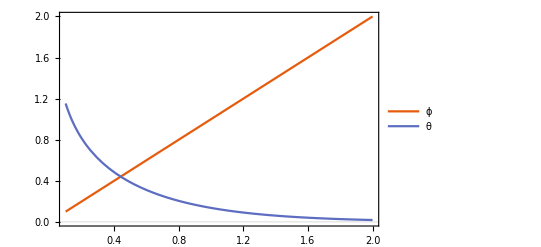

{{J0→0.440687},0.440687,0.440687}

2.26919

```mathematica
Clear["Global`*"];β=1;θ=ArcTanh@Exp[-2β J0];ϕ=β J0;
Plot[{ϕ,θ},{J0,0.1,2},PlotTheme->"Scientific",PlotLegends->"Expressions"]
{FindRoot[ϕ==θ,{J0,0.5}],N@1/2 ArcSinh[1],N@1/2Log[1+√2]}
1/(1/2Log[1+√2])//N
```

## Machine Leaning

## Artificial Neural Networks

```mathematica
Clear["Global`*"];
layerCounts = {3, 4, 6, 6,4 ,2};

graph = GraphUnion @@ 
   MapThread[
    IndexGraph, {CompleteGraph /@ Partition[layerCounts, 2, 1], 
     FoldList[Plus, 0, layerCounts[[;; -3]]]}];
vstyle = 
 Catenate[
  Thread /@ 
   Thread[
    TakeList[VertexList[graph], layerCounts] -> 
     ColorData[97] /@ Range@Length[layerCounts]]];
graph = Graph[
    graph,
    GraphLayout -> {"MultipartiteEmbedding", 
    "VertexPartition" -> layerCounts},
    GraphStyle -> "BasicBlack",
    VertexSize -> 0.5,
    VertexStyle -> vstyle,ImageSize->300
    ];
(*Show[graph, PlotLabel ->  Placed["Input layer                     Hidden layers                   Output layer",Bottom],LabelStyle ->{12,FontFamily -> "Times", Black}]*)
Grid[{{"Input\nlayer",graph,"Output\nlayer"},{Null,"Hidden layers",Null}},BaseStyle->{10,FontFamily -> "Times", Black}]
```

Input
layer | -Graphics- | Output
layer
 | Hidden layers |

## Handwritten Digits

```mathematica
Clear["Global`*"];
trainingData=ResourceData["MNIST","TrainingData"];
testData=ResourceData["MNIST","TestData"];
mnistEncoder=NetEncoder[{"Image",{28,28},"ColorSpace"->"Grayscale"}]
```

NetEncoder[<>]

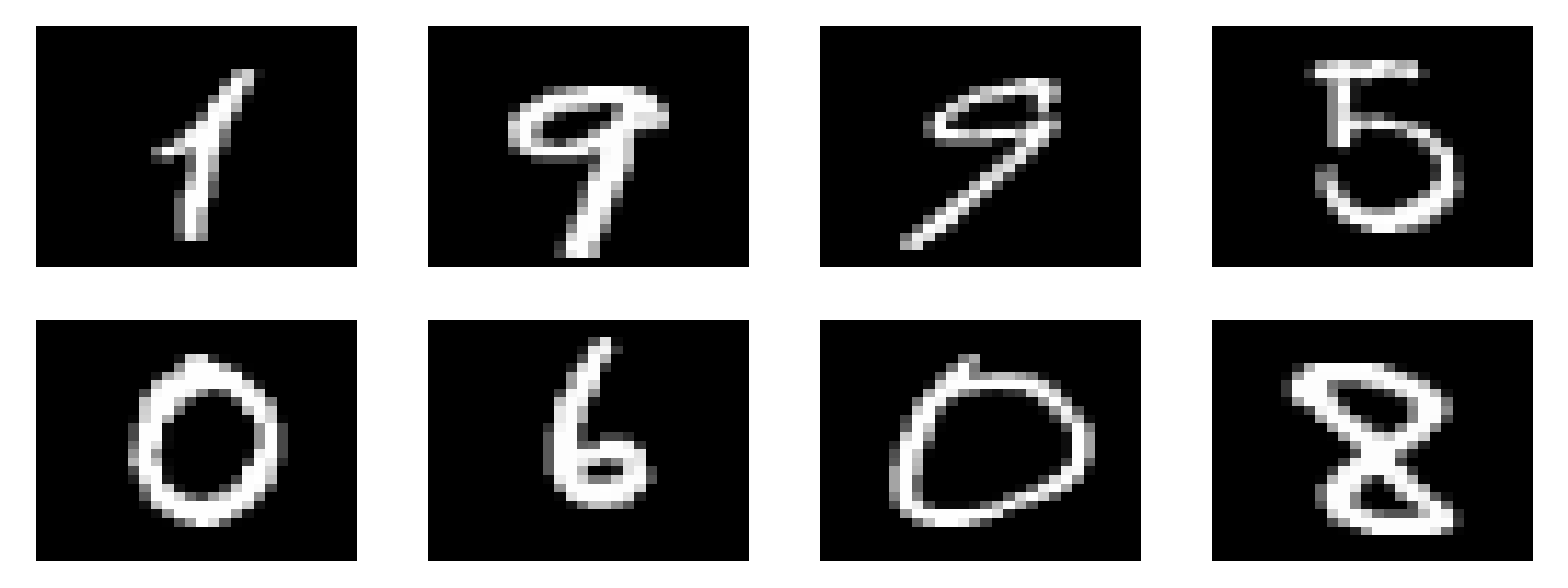

```mathematica
Grid[{ArrayPlot@First@mnistEncoder@trainingData[[#,1]]&/@{7000,59300,60000,32000},ArrayPlot@First@mnistEncoder@trainingData[[#,1]]&/@{3000,38000,1800,52000}}]
```

## Reinforcement Learning

This is a simple demonstration for GridWorld.

### Random Policy

```mathematica
Clear["Global`*"]
𝒮=Flatten[Table[{i,j},{i,5},{j,5}],1];
𝒜={north,south,west,east};
reward[s_,a_]:=Which[s=={1,2},10,s=={1,4},5,s==a@s,-1,True,0]
north[s_]:=Which[s=={1,2},{5,2},s=={1,4},{3,4},True,If[s⟦1⟧>1,s-{1,0},s]]
south[s_]:=Which[s=={1,2},{5,2},s=={1,4},{3,4},True,If[s⟦1⟧<5,s+{1,0},s]]
west[s_]:=Which[s=={1,2},{5,2},s=={1,4},{3,4},True,If[s⟦2⟧>1,s-{0,1},s]]
east[s_]:=Which[s=={1,2},{5,2},s=={1,4},{3,4},True,If[s⟦2⟧<5,s+{0,1},s]]
valueBellman[s_,γ_:0.9]:=value[s]==Sum[1/4(reward[s,a]+γ*value[a@s]),{a,𝒜}]
```

```mathematica
results=NSolve[valueBellman/@𝒮,value/@𝒮]⟦1,All,2⟧;
Grid[Partition[NumberForm[#,{2,1}]&/@results,5],Frame->All]
```

3.3 | 8.8 | 4.4 | 5.3 | 1.5
1.5 | 3.0 | 2.3 | 1.9 | 0.5
0.1 | 0.7 | 0.7 | 0.4 | -0.4
-1.0 | -0.4 | -0.4 | -0.6 | -1.2
-1.9 | -1.3 | -1.2 | -1.4 | -2.0

{{2,3},{2,2},{3,2},{2,2},{3,2},{3,1}}

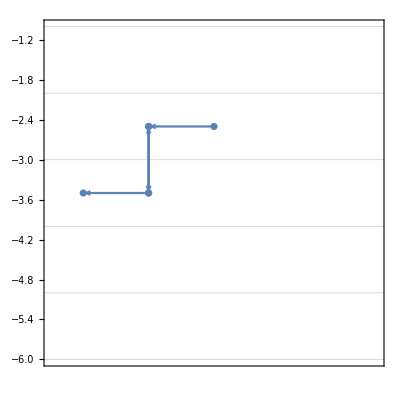

```mathematica
policy[s_]:=RandomChoice@𝒜;
NestList[policy[#][#]&,{2,3},5]
ListPlot[Reverse@#+{0.5,0.5}&/@%,Frame->True,FrameTicks->None,GridLines->Automatic,ScalingFunctions->{None,"Reverse"},Joined->True,Mesh->All,PlotRange->{{1,6},{1,6}},AspectRatio->1]/.
Line[x_]:>(Arrow@Partition[x,2,1])
```

### Optimal Policy

```mathematica
Clear["Global`*"]
𝒮=Flatten[Table[{i,j},{i,5},{j,5}],1];
𝒜={north,south,west,east};
reward[s_,a_]:=Which[s=={1,2},10,s=={1,4},5,s==a@s,-1,True,0]
north[s_]:=Which[s=={1,2},{5,2},s=={1,4},{3,4},True,If[s⟦1⟧>1,s-{1,0},s]]
south[s_]:=Which[s=={1,2},{5,2},s=={1,4},{3,4},True,If[s⟦1⟧<5,s+{1,0},s]]
west[s_]:=Which[s=={1,2},{5,2},s=={1,4},{3,4},True,If[s⟦2⟧>1,s-{0,1},s]]
east[s_]:=Which[s=={1,2},{5,2},s=={1,4},{3,4},True,If[s⟦2⟧<5,s+{0,1},s]]

γ=0.9;Do[value[s]=0.,{s,𝒮}]
Do[value[s]=Max@Table[(reward[s,a]+γ*value[a@s]),{a,𝒜}],100,{s,𝒮}]
Grid[Partition[NumberForm[#,{3,1}]&/@value/@𝒮,5],Frame->All]
```

22.0 | 24.4 | 22.0 | 19.4 | 17.5
19.8 | 22.0 | 19.8 | 17.8 | 16.0
17.8 | 19.8 | 17.8 | 16.0 | 14.4
16.0 | 17.8 | 16.0 | 14.4 | 13.0
14.4 | 16.0 | 14.4 | 13.0 | 11.7

```mathematica
policy[s_]:=Module[{valueList=Table[(reward[s,a]+γ*value[a@s]),{a,𝒜}]},𝒜⟦#⟧&/@Flatten@Position[valueList,Max@valueList]]
Grid[Partition[policy/@𝒮,5],Frame->All]
```

{east} | {north,south,west,east} | {west} | {north,south,west,east} | {west}
{north,east} | {north} | {north,west} | {west} | {west}
{north,east} | {north} | {north,west} | {north,west} | {north,west}
{north,east} | {north} | {north,west} | {north,west} | {north,west}
{north,east} | {north} | {north,west} | {north,west} | {north,west}

# Chapter 2 Quantum Machine Learning in the NISQ Era

## Quantum Algorithms

## Grover Search

```mathematica
OracleGate[input_List]:=Module[{n,matrixRep},n=FromDigits[input,2];
matrixRep=IdentityMatrix[2^Length[input]];
matrixRep[[n+1,n+1]]=-1;
QuantumOperator[matrixRep,QuantumBasis[2,Length[input]],"Label"->"Grover Oracle"]]
GroverCircuit[marker_List]:=QuietEcho@QuantumCircuitOperator[{QuantumOperator[{"H",3},{1,2,3}],OracleGate[marker],QuantumOperator[{"H",3},{1,2,3}],QuantumOperator["PauliX"],QuantumOperator["PauliX",{2}],QuantumOperator["PauliX",{3}],QuantumOperator[{"ControlledU","PauliZ",{2,3}},{1}],QuantumOperator["PauliX"],QuantumOperator["PauliX",{2}],QuantumOperator["PauliX",{3}],QuantumOperator[{"H",3},{1,2,3}],QuantumMeasurementOperator[],QuantumMeasurementOperator[{2}],QuantumMeasurementOperator[{3}]}]
```

```mathematica
GroverCircuit[{1,0,1}]["Diagram",ImageSize->800]
```

-Graphics-

## Quantum Phase Estimation

```mathematica
qc=QuietEcho@QuantumCircuitOperator[ {QuantumOperator[{"H",3},{1,2,3}],QuantumOperator["X",{4}],QuantumOperator[{"CPHASE",1},{3,4}],QuantumOperator[{"CPHASE",2},{2,4}],QuantumOperator[{"CPHASE",4},{1,4}],QuantumOperator[QuantumOperator["InverseFourier",{1,2,3}],"Label"->"QFT^†"],QuantumMeasurementOperator[{1,2,3}]}];
(qc/.{"P"[1]->"U^(2^0)","P"[2]->"U^(2^1)","P"[4]->"U^(2^2)"})["Diagram",ImageSize->600]
```

-Graphics-

# Chapter 3 Quantum Architecture Search

## Neuroevolution of Augmenting Topologies Algorithm

```mathematica
Clear["Global`*"]
(*the iconized original dataset*)
{accTestHistory,accTrainHistory,lossTestHistory,lossTrainHistory,bestInEachGeneration,populations}={,,,,,};
```

```mathematica
lenGens=Length@bestInEachGeneration;
optionGeneration=Sequence[FrameStyle->Directive[Black,Thick],Frame->True,FrameTicks->{{Automatic,None},{Range@lenGens,None}},FrameLabel->{"Generations","Fitness"},GridLines->{Range@lenGens,None},BaseStyle->{FontFamily->"Times",Black,18},ImagePadding->{{50,10},{50,10}},ImageSize->{350,240}];
Show[ListPolarPlot[{2π(Range@lenGens-1)/lenGens,bestInEachGeneration}ᵀ,PlotRange->1.25,Joined->True,PolarAxes->True,PlotStyle->RGBColor[0.9058823529411765, 0.027450980392156862, 0.12941176470588237], PolarAxesOrigin->{0,0},PolarGridLines->{2π(Range@lenGens-1)/lenGens,Automatic},PolarTicks->{{2π(Range@lenGens-1)/lenGens,ToString/@Range@lenGens}ᵀ,Automatic},Epilog->{Arrow[{{0.2,1.05},{-0.2,1.05}}],Text["Generations",{0,1.2}],Arrow[{{0.5,-0.15},{0.9,-0.15}}],Text["Fitness",{0.65,-0.2}]},BaseStyle->{FontFamily->"Times",Black,14}],ListPolarPlot[{2π(populations[[All,1]]-1)/lenGens,populations[[All,2]]}ᵀ,PlotStyle->RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824]],ImageSize->400]
```

-Graphics-

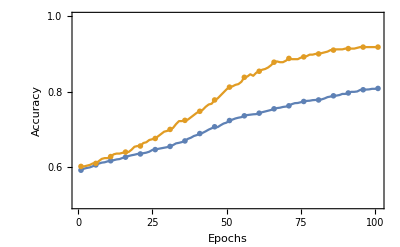
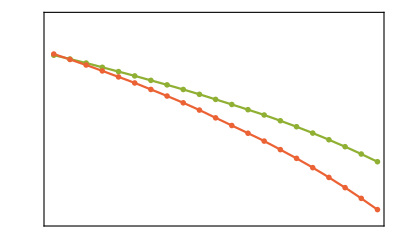

```mathematica
optionEpoch=Sequence[FrameStyle->Directive[Black,Thick],ImagePadding->{{50,60},{50,10}},BaseStyle->{FontFamily->"Times",Black,18},ImageSize->400];
accuPlot=Show[ListLinePlot[{accTrainHistory,accTestHistory},PlotStyle->ColorData[97,"ColorList"][[1;;2]],PlotRange->{0.5,1.0},Frame->{True,True,True,False},FrameTicks->{{{0.4,0.5,0.6,0.7,0.8,0.9,{1,"1.0"}},None},{Automatic,None}},FrameLabel->{{"Accuracy","Epochs"},{"Epochs",None}},optionEpoch],
ListPlot[{accTrainHistory,accTestHistory}ᵀ[[1;;;;5]]ᵀ,DataRange->{1,Length@accTrainHistory},PlotMarkers->"OpenMarkers"]];
lossPlot=Show[ListLinePlot[{lossTrainHistory,lossTestHistory},PlotStyle->ColorData[97,"ColorList"][[3;;4]],PlotRange->{0.6,0.7},Frame->{False,False,False,True},FrameTicks->{{None,All},{None,None}},FrameLabel->{{None,"Loss"},{None,None}},optionEpoch],
ListPlot[{lossTrainHistory,lossTestHistory}ᵀ[[1;;;;5]]ᵀ,DataRange->{1,Length@accTrainHistory},PlotStyle->ColorData[97,"ColorList"][[3;;4]],PlotMarkers->Charting`CommonDump`GraphicsOpenPlotMarkers[][[3;;4]]]];
accuLegend=Framed[LineLegend[ColorData[97,"ColorList"][[1;;2]],{"training accuracy","validation accuracy"},LegendMarkers->"OpenMarkers",LabelStyle->{FontFamily->"Times",14}],FrameStyle->GrayLevel[0, 0],ImageSize->{280,190},Alignment->{Right,Bottom}];
lossLegend=Framed[LineLegend[ColorData[97,"ColorList"][[3;;4]],{"training loss","validation loss"},LegendMarkers->Charting`CommonDump`GraphicsOpenPlotMarkers[][[3;;4]],LabelStyle->{FontFamily->"Times",14},LegendMargins->0],FrameStyle->GrayLevel[0, 0],ImageSize->{220,60},Alignment->{Right,Bottom}];
gene1Epoch=Overlay[{accuPlot,lossPlot,accuLegend,lossLegend}]
```

## Markovian NeuroEvolution Algorithm

## Graph-Encoding

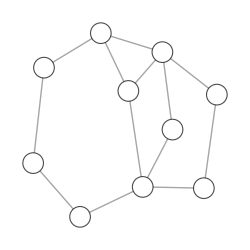

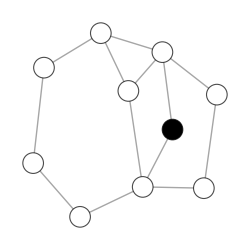

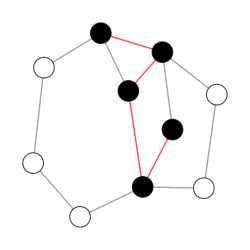

```mathematica
selectEdges=;allEdges=;
Graph[Join[Style[#,GrayLevel[0.5]]&/@selectEdges,Style[#,GrayLevel[0.5]]&/@allEdges]/.{x_,y_}:>x->y,VertexStyle->GrayLevel[1],VertexSize->0.4,ImageSize->250,AspectRatio->1,EdgeShapeFunction->"CarvedArcArrow",EdgeStyle->Thick,BaseStyle->EdgeForm[Thick]]
Graph[{Style[selectEdges[[1,1]],{GrayLevel[0],25}]},Join[Style[#,GrayLevel[0.5]]&/@selectEdges,Style[#,GrayLevel[0.5]]&/@allEdges]/.{x_,y_}:>x->y,VertexStyle->GrayLevel[1],VertexSize->0.4,ImageSize->250,AspectRatio->1,EdgeShapeFunction->"CarvedArcArrow",EdgeStyle->Thick,BaseStyle->EdgeForm[Thick]]
Graph[Style[#,GrayLevel[0]]&/@DeleteDuplicates@Flatten@selectEdges,Join[Style[#,Red]&/@selectEdges,Style[#,GrayLevel[0.5]]&/@allEdges]/.{x_,y_}:>x->y,VertexStyle->GrayLevel[1],VertexSize->0.4,ImageSize->250,AspectRatio->1,EdgeShapeFunction->"CarvedArcArrow",EdgeStyle->Thick,BaseStyle->EdgeForm[Thick]]
```

## Classification of Handwritten-Digit Images

```mathematica
Clear["Global`*"]
(*the iconized numerical results obtained by random initial variational parameters*)
{accTestHistory,accTrainHistory,lossTestHistory,lossTrainHistory,bestInEachGeneration,populations}={,,,,,};
```

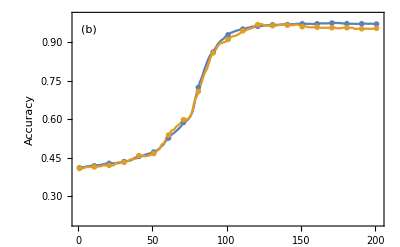
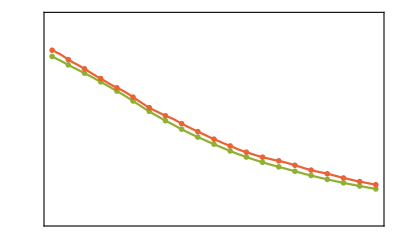

```mathematica
optionEpoch=Sequence[FrameStyle->Directive[Black,Thick],ImagePadding->{{55,60},{20,10}},BaseStyle->{FontFamily->"Times",Black,20},ImageSize->400];
accuPlot=Show[ListLinePlot[{accTrainHistory,accTestHistory},PlotStyle->ColorData[97,"ColorList"][[1;;2]],PlotRange->{0.2,1.0},Frame->{True,True,True,False},FrameLabel->{{"Accuracy",None},{None,None}},optionEpoch],
ListPlot[{accTrainHistory,accTestHistory}ᵀ[[1;;;;10]]ᵀ,DataRange->{1,201},PlotMarkers->"OpenMarkers"],Epilog->Text["(b)",{7,0.95}]];
lossPlot=Show[ListLinePlot[{lossTrainHistory,lossTestHistory},PlotStyle->ColorData[97,"ColorList"][[3;;4]],PlotRange->{0.5,0.78},Frame->{False,False,False,True},FrameTicks->{{None,All},{None,None}},FrameLabel->{{None,"Loss"},{None,None}},optionEpoch],
ListPlot[{lossTrainHistory,lossTestHistory}ᵀ[[1;;;;10]]ᵀ,DataRange->{1,201},PlotStyle->ColorData[97,"ColorList"][[3;;4]],PlotMarkers->Charting`CommonDump`GraphicsOpenPlotMarkers[][[3;;4]]]];
accuLegend=Framed[LineLegend[ColorData[97,"ColorList"][[1;;2]],{"training accuracy","validation accuracy"},LegendMarkers->"OpenMarkers","Spacings"->0.1,LabelStyle->{FontFamily->"Times",20}],FrameStyle->GrayLevel[0, 0],ImageSize->{285,195},Alignment->{Right,Bottom}];
lossLegend=Framed[LineLegend[ColorData[97,"ColorList"][[3;;4]],{"training loss","validation loss"},LegendMarkers->Charting`CommonDump`GraphicsOpenPlotMarkers[][[3;;4]],"Spacings"->0.1,LabelStyle->{FontFamily->"Times",20},LegendMargins->0],FrameStyle->GrayLevel[0, 0],ImageSize->{335,100},Alignment->{Right,Bottom}];
mnist1Epoch=Overlay[{accuPlot,lossPlot,accuLegend,lossLegend}]
```

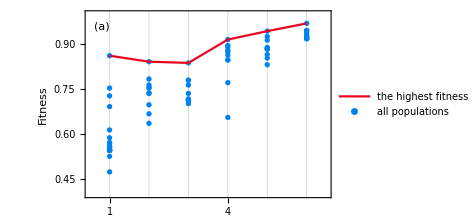

```mathematica
optionGeneration=Sequence[FrameStyle->Directive[Black,Thick],Frame->True,FrameTicks->{{Automatic,None},{Range[13],None}},FrameLabel->{None,"Fitness"},GridLines->{Range[13],None},BaseStyle->{FontFamily->"Times",Black,20},ImagePadding->{{55,10},{20,10}},ImageSize->{350,240}];
mnist1Generation=Show[ListPlot[populations,PlotStyle->RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],PlotRange->{{0.5,6.5},{0.4,1}},optionGeneration,PlotLegends->Placed[LineLegend[{RGBColor[0.9058823529411765, 0.027450980392156862, 0.12941176470588237],RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824]},{"the highest fitness","all populations"},LabelStyle->{FontFamily->"Times",20},Joined->{True,False},"Spacings"->0.1(*,LegendFunction->"Panel"*)],{0.65,0.2}]],ListLinePlot[bestInEachGeneration,PlotStyle->RGBColor[0.9058823529411765, 0.027450980392156862, 0.12941176470588237]],Epilog->Text["(a)",{0.8,0.96}]]
```

```mathematica
(*the iconized numerical results obtained by fixed initial variational parameters*)
{accTestHistory,accTrainHistory,lossTestHistory,lossTrainHistory,bestInEachGeneration,populations}{,,,,,}
```

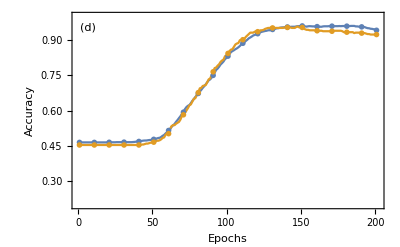
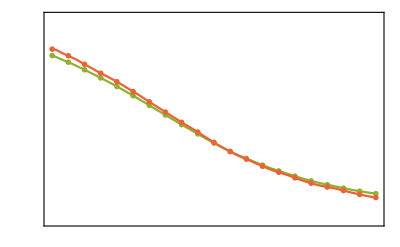

```mathematica
optionEpoch=Sequence[FrameStyle->Directive[Black,Thick],ImagePadding->{{55,60},{50,10}},BaseStyle->{FontFamily->"Times",Black,20},ImageSize->400];
accuPlot=Show[ListLinePlot[{accTrainHistory,accTestHistory},PlotStyle->ColorData[97,"ColorList"][[1;;2]],PlotRange->{0.2,1.0},Frame->{True,True,True,False},FrameLabel->{{"Accuracy",None},{"Epochs",None}},optionEpoch],
ListPlot[{accTrainHistory,accTestHistory}ᵀ[[1;;;;10]]ᵀ,DataRange->{1,201},PlotMarkers->"OpenMarkers"],Epilog->Text["(d)",{7,0.95}]];
lossPlot=Show[ListLinePlot[{lossTrainHistory,lossTestHistory},PlotStyle->ColorData[97,"ColorList"][[3;;4]],PlotRange->{0.5,0.75},Frame->{False,False,False,True},FrameTicks->{{None,All},{None,None}},FrameLabel->{{None,"Loss"},{None,None}},optionEpoch],
ListPlot[{lossTrainHistory,lossTestHistory}ᵀ[[1;;;;10]]ᵀ,DataRange->{1,201},PlotStyle->ColorData[97,"ColorList"][[3;;4]],PlotMarkers->Charting`CommonDump`GraphicsOpenPlotMarkers[][[3;;4]]]];
accuLegend=Framed[LineLegend[ColorData[97,"ColorList"][[1;;2]],{"training accuracy","validation accuracy"},LegendMarkers->"OpenMarkers","Spacings"->0.1,LabelStyle->{FontFamily->"Times",20}],FrameStyle->GrayLevel[0, 0],ImageSize->{265,195},Alignment->{Right,Bottom}];
lossLegend=Framed[LineLegend[ColorData[97,"ColorList"][[3;;4]],{"training loss","validation loss"},LegendMarkers->Charting`CommonDump`GraphicsOpenPlotMarkers[][[3;;4]],"Spacings"->0.1,LabelStyle->{FontFamily->"Times",20},LegendMargins->0],FrameStyle->GrayLevel[0, 0],ImageSize->{335,112},Alignment->{Right,Bottom}];
mnist2Epoch=Overlay[{accuPlot,lossPlot,accuLegend,lossLegend}]
```

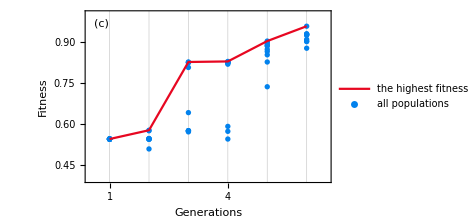

```mathematica
optionGeneration=Sequence[FrameStyle->Directive[Black,Thick],Frame->True,FrameTicks->{{Automatic,None},{Range[13],None}},FrameLabel->{"Generations","Fitness"},GridLines->{Range@Length[bestInEachGeneration],None},BaseStyle->{FontFamily->"Times",Black,20},ImagePadding->{{55,10},{50,10}},ImageSize->{350,240}];
 mnist2Generation=Show[ListPlot[populations,PlotStyle->RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],PlotRange->{{0.5,6.5},{0.4,1}},optionGeneration,PlotLegends->Placed[LineLegend[{RGBColor[0.9058823529411765, 0.027450980392156862, 0.12941176470588237],RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824]},{"the highest fitness","all populations"},LabelStyle->{FontFamily->"Times",20},"Spacings"->0.1,Joined->{True,False}(*,LegendFunction->"Panel"*)],{0.38,0.82}]],ListLinePlot[bestInEachGeneration,PlotStyle->RGBColor[0.9058823529411765, 0.027450980392156862, 0.12941176470588237]],Epilog->Text["(c)",{0.8,0.965}]]
```

```mathematica
Grid[{{mnist1Generation,mnist1Epoch},{mnist2Generation,mnist2Epoch}},Spacings->{1,-0.4}]
```

-Graphics- | -Graphics--Graphics-
-Graphics- | -Graphics--Graphics-

## Classification of Symmetry-Protected Topological States

```mathematica
Clear["Global`*"]
(*the iconized numerical results obtained by random initial variational parameters*)
{accTestHistory,accTrainHistory,lossTestHistory,lossTrainHistory,bestInEachGeneration,populations}={,,,,,};
```

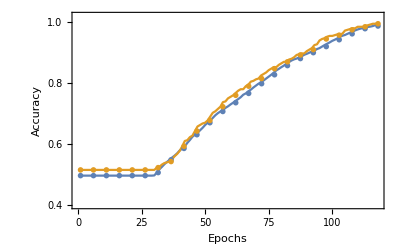
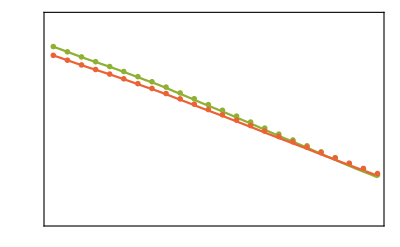

```mathematica
fontsize=14;
optionEpoch=Sequence[FrameStyle->Directive[Black,Thick],ImagePadding->{{50,60},{50,10}},BaseStyle->{FontFamily->"Times",Black,fontsize},ImageSize->400];
accuPlot=Show[ListLinePlot[{accTrainHistory,accTestHistory},PlotStyle->ColorData[97,"ColorList"][[1;;2]],PlotRange->{0.4,1.02},Frame->{True,True,True,False},FrameTicks->{{{0.4,0.5,0.6,0.7,0.8,0.9,{1,"1.0"}},None},{Automatic,None}},FrameLabel->{{"Accuracy","Epochs"},{"Epochs",None}},optionEpoch],
ListPlot[{accTrainHistory,accTestHistory}ᵀ[[1;;;;5]]ᵀ,DataRange->{1,Length@accTrainHistory},PlotMarkers->"OpenMarkers"]];
lossPlot=Show[ListLinePlot[{lossTrainHistory,lossTestHistory},PlotStyle->ColorData[97,"ColorList"][[3;;4]],PlotRange->{0.55,0.70},Frame->{False,False,False,True},FrameTicks->{{None,All},{None,None}},FrameLabel->{{None,"Loss"},{None,None}},optionEpoch],
ListPlot[{lossTrainHistory,lossTestHistory}ᵀ[[1;;;;5]]ᵀ,DataRange->{1,Length@accTrainHistory},PlotStyle->ColorData[97,"ColorList"][[3;;4]],PlotMarkers->Charting`CommonDump`GraphicsOpenPlotMarkers[][[3;;4]]]];
accuLegend=Framed[LineLegend[ColorData[97,"ColorList"][[1;;2]],{"training accuracy","validation accuracy"},"Spacings"->0.1,LegendMarkers->"OpenMarkers",LabelStyle->{FontFamily->"Times",fontsize}],FrameStyle->GrayLevel[0, 0],ImageSize->{320,190},Alignment->{Right,Bottom}];
lossLegend=Framed[LineLegend[ColorData[97,"ColorList"][[3;;4]],{"training loss","validation loss"},"Spacings"->0.1,LegendMarkers->Charting`CommonDump`GraphicsOpenPlotMarkers[][[3;;4]],LabelStyle->{FontFamily->"Times",fontsize},LegendMargins->0],FrameStyle->GrayLevel[0, 0],ImageSize->{240,60},Alignment->{Right,Bottom}];
spt1Epoch=Overlay[{accuPlot,lossPlot,accuLegend,lossLegend}]
```

```mathematica
lenGens=Length@bestInEachGeneration;
Show[ListPolarPlot[{2π(Range@lenGens-1)/lenGens,bestInEachGeneration}ᵀ,PlotRange->1.2,Joined->True,PolarAxes->True,PlotStyle->RGBColor[0.9058823529411765, 0.027450980392156862, 0.12941176470588237], PolarAxesOrigin->{0,0},PolarGridLines->{2π(Range@lenGens-1)/lenGens,Automatic},PolarTicks->{{2π(Range@lenGens-1)/lenGens,ToString/@Range@lenGens}ᵀ,Automatic},Epilog->{Arrow[{{0.2,1.05},{-0.2,1.05}}],Text["Generations",{0,1.15}],Arrow[{{0.5,-0.15},{0.9,-0.15}}],Text["Fitness",{0.65,-0.2}]},BaseStyle->{FontFamily->"Times",Black,14}],ListPolarPlot[{2π(populations[[All,1]]-1)/lenGens,populations[[All,2]]}ᵀ,PlotStyle->RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824]],ImageSize->350]
```

-Graphics-

```mathematica
(*the iconized numerical results obtained by fixed initial variational parameters*)
{accTestHistory,accTrainHistory,lossTestHistory,lossTrainHistory,bestInEachGeneration,populations}={,,,,,};
```

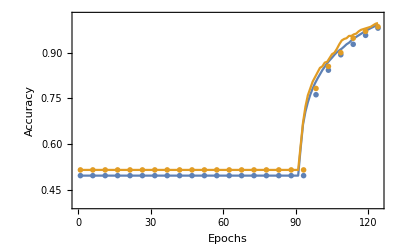
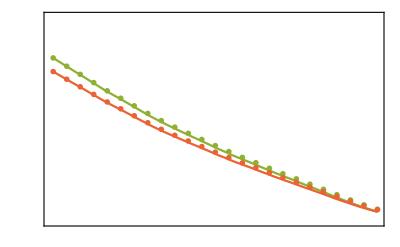

```mathematica
fontsize=14;
optionEpoch=Sequence[FrameStyle->Directive[Black,Thick],ImagePadding->{{50,60},{50,10}},BaseStyle->{FontFamily->"Times",Black,fontsize},ImageSize->400];
accuPlot=Show[ListLinePlot[{accTrainHistory,accTestHistory},PlotStyle->ColorData[97,"ColorList"][[1;;2]],PlotRange->{0.4,1.02},Frame->{True,True,True,False},FrameTicks->Automatic,FrameLabel->{{"Accuracy","Epochs"},{"Epochs",None}},optionEpoch],
ListPlot[{accTrainHistory,accTestHistory}ᵀ[[1;;;;5]]ᵀ,DataRange->{1,Length@accTrainHistory},PlotMarkers->"OpenMarkers"]];
lossPlot=Show[ListLinePlot[{lossTrainHistory,lossTestHistory},PlotStyle->ColorData[97,"ColorList"][[3;;4]],PlotRange->{0.65,0.8},Frame->{False,False,False,True},FrameTicks->{{None,All},{None,None}},FrameLabel->{{None,"Loss"},{None,None}},optionEpoch],
ListPlot[{lossTrainHistory,lossTestHistory}ᵀ[[1;;;;5]]ᵀ,DataRange->{1,Length@accTrainHistory},PlotStyle->ColorData[97,"ColorList"][[3;;4]],PlotMarkers->Charting`CommonDump`GraphicsOpenPlotMarkers[][[3;;4]]]];
accuLegend=Framed[LineLegend[ColorData[97,"ColorList"][[1;;2]],{"training accuracy","validation accuracy"},LegendMarkers->"OpenMarkers",LabelStyle->{FontFamily->"Times",fontsize},"Spacings"->0.1],FrameStyle->GrayLevel[0, 0],ImageSize->{220,60},Alignment->{Right,Bottom}];
lossLegend=Framed[LineLegend[ColorData[97,"ColorList"][[3;;4]],{"training loss","validation loss"},LegendMarkers->Charting`CommonDump`GraphicsOpenPlotMarkers[][[3;;4]],LabelStyle->{FontFamily->"Times",fontsize},"Spacings"->0.1,LegendMargins->0],FrameStyle->GrayLevel[0, 0],ImageSize->{260,90},Alignment->{Right,Bottom}];
spt2Epoch=Overlay[{accuPlot,lossPlot,accuLegend,lossLegend}]
```

```mathematica
lenGens=Length@bestInEachGeneration;
Show[ListPolarPlot[{2π(Range@lenGens-1)/lenGens,bestInEachGeneration}ᵀ,PlotRange->1.2,Joined->True,PolarAxes->True,PlotStyle->RGBColor[0.9058823529411765, 0.027450980392156862, 0.12941176470588237], PolarAxesOrigin->{0,0},PolarGridLines->{2π(Range@lenGens-1)/lenGens,Automatic},PolarTicks->{{2π(Range@lenGens-1)/lenGens,ToString/@Range@lenGens}ᵀ,Automatic},Epilog->{Arrow[{{0.2,1.05},{-0.2,1.05}}],Text["Generations",{0,1.15}],Arrow[{{0.5,-0.15},{0.9,-0.15}}],Text["Fitness",{0.65,-0.2}]},BaseStyle->{FontFamily->"Times",Black,14}],ListPolarPlot[{2π(populations[[All,1]]-1)/lenGens,populations[[All,2]]}ᵀ,PlotStyle->RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824]],ImageSize->350]
```

-Graphics-

## Classification of Cancer Diagnostic Data

```mathematica
Clear["Global`*"]
(*the iconized numerical results obtained by random initial variational parameters*)
{accTestHistory,accTrainHistory,lossTestHistory,lossTrainHistory,bestInEachGeneration,populations}={,,,,,};
```

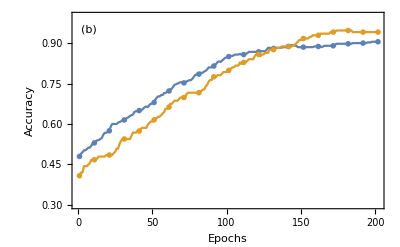
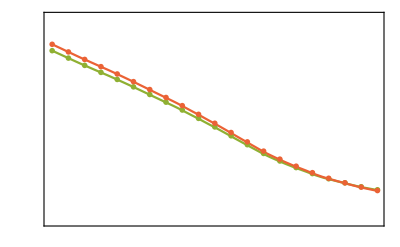

```mathematica
optionEpoch=Sequence[FrameStyle->Directive[Black,Thick],ImagePadding->{{55,60},{50,10}},BaseStyle->{FontFamily->"Times",Black,20},ImageSize->400];
accuPlot=Show[ListLinePlot[{accTrainHistory,accTestHistory},PlotStyle->ColorData[97,"ColorList"][[1;;2]],PlotRange->{0.3,1.0},Frame->{True,True,True,False}(*,FrameTicks->{{{0.7,0.8,0.9,{1,"1.0"}},None},{Automatic,None}}*),FrameLabel->{{"Accuracy","Epochs"},{"Epochs",None}},optionEpoch],
ListPlot[{accTrainHistory,accTestHistory}ᵀ[[1;;;;10]]ᵀ,DataRange->{1,Length@accTrainHistory},PlotMarkers->"OpenMarkers"],Epilog->Text["(b)",{7,0.95}]];
lossPlot=Show[ListLinePlot[{lossTrainHistory,lossTestHistory},PlotStyle->ColorData[97,"ColorList"][[3;;4]],PlotRange->{0.3,0.8},Frame->{False,False,False,True},FrameTicks->{{None,All},{None,None}},FrameLabel->{{None,"Loss"},{None,None}},optionEpoch],
ListPlot[{lossTrainHistory,lossTestHistory}ᵀ[[1;;;;10]]ᵀ,DataRange->{1,Length@accTrainHistory},PlotStyle->ColorData[97,"ColorList"][[3;;4]],PlotMarkers->Charting`CommonDump`GraphicsOpenPlotMarkers[][[3;;4]]]];
accuLegend=Framed[LineLegend[ColorData[97,"ColorList"][[1;;2]],{"training accuracy","validation accuracy"},LegendMarkers->"OpenMarkers",LabelStyle->{FontFamily->"Times",20},"Spacings"->0.1],FrameStyle->GrayLevel[0, 0],ImageSize->{280,190},Alignment->{Right,Bottom}];
lossLegend=Framed[LineLegend[ColorData[97,"ColorList"][[3;;4]],{"training loss","validation loss"},LegendMarkers->Charting`CommonDump`GraphicsOpenPlotMarkers[][[3;;4]],LabelStyle->{FontFamily->"Times",20},LegendMargins->0,"Spacings"->0.1],FrameStyle->GrayLevel[0, 0],ImageSize->{342,110},Alignment->{Right,Bottom}];
cancer1Epoch=Overlay[{accuPlot,lossPlot,accuLegend,lossLegend}]
```

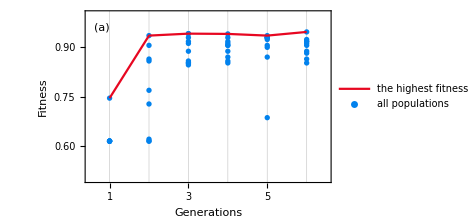

```mathematica
optionGeneration=Sequence[FrameStyle->Directive[Black,Thick],Frame->True,FrameTicks->{{Automatic,None},{Range@Length@bestInEachGeneration,None}},FrameLabel->{"Generations","Fitness"},GridLines->{Range@Length@bestInEachGeneration,None},BaseStyle->{FontFamily->"Times",Black,20},ImagePadding->{{55,10},{50,10}},ImageSize->{350,240}];
cancer1Generation=Show[ListPlot[populations,PlotStyle->RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],PlotRange->{{0.5,6.5},{0.5,1}},optionGeneration,PlotLegends->Placed[LineLegend[{RGBColor[0.9058823529411765, 0.027450980392156862, 0.12941176470588237],RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824]},{"the highest fitness","all populations"},LabelStyle->{FontFamily->"Times",20},"Spacings"->0.1,Joined->{True,False}],{0.65,0.20}]],ListLinePlot[bestInEachGeneration,PlotStyle->RGBColor[0.9058823529411765, 0.027450980392156862, 0.12941176470588237],PlotRange->All],Epilog->Text["(a)",{0.8,0.96}]]
```

```mathematica
(*the iconized numerical results obtained by fixed initial variational parameters*)
{accTestHistory,accTrainHistory,lossTestHistory,lossTrainHistory,bestInEachGeneration,populations}={,,,,,};
```

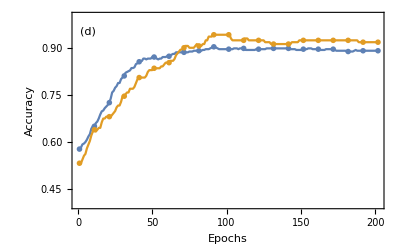
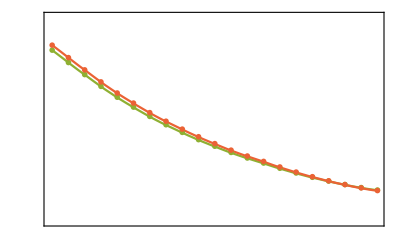

```mathematica
optionEpoch=Sequence[FrameStyle->Directive[Black,Thick],ImagePadding->{{55,60},{50,10}},BaseStyle->{FontFamily->"Times",Black,20},ImageSize->400];
accuPlot=Show[ListLinePlot[{accTrainHistory,accTestHistory},PlotStyle->ColorData[97,"ColorList"][[1;;2]],PlotRange->{0.4,1.0},Frame->{True,True,True,False},FrameLabel->{{"Accuracy","Epochs"},{"Epochs",None}},optionEpoch],
ListPlot[{accTrainHistory,accTestHistory}ᵀ[[1;;;;10]]ᵀ,DataRange->{1,Length@accTrainHistory},PlotMarkers->"OpenMarkers"],Epilog->Text["(d)",{7,0.95}]];
lossPlot=Show[ListLinePlot[{lossTrainHistory,lossTestHistory},PlotStyle->ColorData[97,"ColorList"][[3;;4]],PlotRange->{0.35,0.75},Frame->{False,False,False,True},FrameTicks->{{None,All},{None,None}},FrameLabel->{{None,"Loss"},{None,None}},optionEpoch],
ListPlot[{lossTrainHistory,lossTestHistory}ᵀ[[1;;;;10]]ᵀ,DataRange->{1,Length@accTrainHistory},PlotStyle->ColorData[97,"ColorList"][[3;;4]],PlotMarkers->Charting`CommonDump`GraphicsOpenPlotMarkers[][[3;;4]]]];
accuLegend=Framed[LineLegend[ColorData[97,"ColorList"][[1;;2]],{"training accuracy","validation accuracy"},LegendMarkers->"OpenMarkers",LabelStyle->{FontFamily->"Times",20},"Spacings"->0.1],FrameStyle->GrayLevel[0, 0],ImageSize->{265,195},Alignment->{Right,Bottom}];
lossLegend=Framed[LineLegend[ColorData[97,"ColorList"][[3;;4]],{"training loss","validation loss"},LegendMarkers->Charting`CommonDump`GraphicsOpenPlotMarkers[][[3;;4]],LabelStyle->{FontFamily->"Times",20},"Spacings"->0.1,LegendMargins->0],FrameStyle->GrayLevel[0, 0],ImageSize->{330,110},Alignment->{Right,Bottom}];
cancer2Epoch=Overlay[{accuPlot,lossPlot,accuLegend,lossLegend}]
```

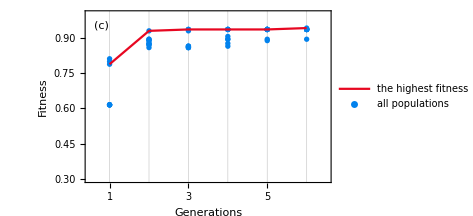

```mathematica
optionGeneration=Sequence[FrameStyle->Directive[Black,Thick],Frame->True,FrameTicks->{{Automatic,None},{Range@Length@bestInEachGeneration,None}},FrameLabel->{"Generations","Fitness"},GridLines->{Range@Length@bestInEachGeneration,None},BaseStyle->{FontFamily->"Times",Black,20},ImagePadding->{{55,10},{50,10}},ImageSize->{350,240}];
 cancer2Generation=Show[ListPlot[populations,PlotStyle->RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],PlotRange->{{0.5,6.5},{0.3,1}},optionGeneration,PlotLegends->Placed[LineLegend[{RGBColor[0.9058823529411765, 0.027450980392156862, 0.12941176470588237],RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824]},{"the highest fitness","all populations"},LabelStyle->{FontFamily->"Times",20},"Spacings"->0.1,Joined->{True,False}],{0.65,0.20}]],ListLinePlot[bestInEachGeneration,PlotStyle->RGBColor[0.9058823529411765, 0.027450980392156862, 0.12941176470588237],PlotRange->All],Epilog->Text["(c)",{0.8,0.95}]]
```

```mathematica
Grid[{{cancer1Generation,cancer1Epoch},{cancer2Generation,cancer2Epoch}},Spacings->{1,-0.4}]
```

-Graphics- | -Graphics--Graphics-
-Graphics- | -Graphics--Graphics-

# Chapter 4 Information Processing in Quantum Spin Chains

## Wavefunctions Near the Critical Points

## Expressions

### General

```mathematica
Clear["Global`*","SubPlus","SubMinus","Subscript"];
uM[x_]:=+IE*Exp[+ⅈ SubPlus[KN] x]+RE*Exp[-ⅈ SubPlus[KN] x];
vM[x_]:=+IH*Exp[-ⅈ SubMinus[KN] x]+RH*Exp[+ⅈ SubMinus[KN] x];
u[x_]:=ⅇ^(-ⅈ ϕ)(+C1*Cos[U]*Exp[+SubPlus[KS]x]+C2*Sin[V]*Exp[+SubMinus[KS]x]+C3*Cos[U]*Exp[-SubPlus[KS]x]+C4*Sin[V]*Exp[-SubMinus[KS]x]);
v[x_]:=ⅇ^(+ⅈ ϕ)(-C1*Cos[V]*Exp[+SubPlus[KS]x]-C2*Sin[U]*Exp[+SubMinus[KS]x]+C3*Cos[V]*Exp[-SubPlus[KS]x]+C4*Sin[U]*Exp[-SubMinus[KS]x]);

Ξ=t ϵ/(2J);Γ=2 γ^2;Ω=t(2t+g);Λ=√(Γ^2+Ξ^2-2Γ Ω);
U=ArcCos[(Λ-Ξ)/Γ]/2;V=ArcCos[(Λ+Ξ)/Γ]/2;
SubPlus[KS]=2 γ Cos[U] Cos[V]/(t a);(*√(Γ-Ω+Λ)/(t a)*)SubMinus[KS]=2 γ Sin[U] Sin[V]/(t a);(*√(Γ-Ω-Λ)/(t a)*)
SubPlus[KN]=2 γ Sin[U]Cos[V]/(t a);(*√(Ω+Ξ)/(t a)*)SubMinus[KN]=2 γ Cos[U]Sin[V]/(t a);(*√(Ω-Ξ)/(t a)*)

ruleNM={J->1.1,a->0.9,t->1,γ->0.9,g->-1.9,ϵ->0.1,λ->1.1,ϕ->7,L->10};
Chop@Simplify[{
t*a^2*uM''[x]+(2t+g+ϵ/(2J))*uM[x],
t*a^2*vM''[x]+(2t+g-ϵ/(2J))*vM[x],
t*a^2*u''[x]+2γ a ⅇ^(-2ⅈ ϕ)*v'[x]+(2t+g+ϵ/(2J))*u[x],
t*a^2*v''[x]+2γ a ⅇ^(+2ⅈ ϕ)*u'[x]+(2t+g-ϵ/(2J))*v[x]}/.ruleNM]
```

{0,0,0,0}

### Left-Middle-Right

```mathematica
Clear["Global`*"];Clear["SubPlus","SubMinus"];
ruleNM={J->1.1,a->0.9,t->1,γ->0.9,g->-1.9,ϵ->0.1,λ->1.1,ϕ->7,L->10};
Ξ=t ϵ/(2J);Γ=2 γ^2;Ω=t(2t+g);Λ=√(Γ^2+Ξ^2-2Γ Ω);
U=ArcCos[(Λ-Ξ)/Γ]/2;V=ArcCos[(Λ+Ξ)/Γ]/2;
SubPlus[KS]=2 γ Cos[U] Cos[V]/(t a);SubMinus[KS]=2 γ Sin[U] Sin[V]/(t a);SubPlus[KN]=2 γ Sin[U]Cos[V]/(t a);SubMinus[KN]=2 γ Cos[U]Sin[V]/(t a);
uL[x_]:=+C1*Cos[U]*Exp[+SubPlus[KS]x]+C2*Sin[V]*Exp[+SubMinus[KS]x];
vL[x_]:=-C1*Cos[V]*Exp[+SubPlus[KS]x]-C2*Sin[U]*Exp[+SubMinus[KS]x];
uM[x_]:=+C5*Exp[+ⅈ SubPlus[KN] x]+C6*Exp[-ⅈ SubPlus[KN] x];
vM[x_]:=+C7*Exp[+ⅈ SubMinus[KN] x]+C8*Exp[-ⅈ SubMinus[KN] x];
uR[x_]:=ⅇ^(-ⅈ ϕ)(C3*Cos[U]*Exp[-SubPlus[KS]x]+C4*Sin[V]*Exp[-SubMinus[KS]x]);
vR[x_]:=ⅇ^(+ⅈ ϕ)(C3*Cos[V]*Exp[-SubPlus[KS]x]+C4*Sin[U]*Exp[-SubMinus[KS]x]);
Chop@Simplify[{
t*a^2*uL''[x]+2γ*a*vL'[x]+(2t+g+ϵ/(2J))*uL[x],
t*a^2*vL''[x]+2γ*a*uL'[x]+(2t+g-ϵ/(2J))*vL[x],
t*a^2*uM''[x]+(2t+g+ϵ/(2J))*uM[x],
t*a^2*vM''[x]+(2t+g-ϵ/(2J))*vM[x],
t*a^2*uR''[x]+2γ*a*ⅇ^(-2ⅈ  ϕ)*vR'[x]+(2t+g+ϵ/(2J))*uR[x],
t*a^2*vR''[x]+2γ*a*ⅇ^(+2ⅈ  ϕ)*uR'[x]+(2t+g-ϵ/(2J))*vR[x]}/.ruleNM]
```

{0,0,0,0,0,0}

## Scattering Matrices

### Right Junction

```mathematica
Clear["Global`*","SubPlus","SubMinus","Subscript"];
uM[x_]:=+IE*Exp[+ⅈ SubPlus[KN] x]+RE*Exp[-ⅈ SubPlus[KN] x];
vM[x_]:=+IH*Exp[-ⅈ SubMinus[KN] x]+RH*Exp[+ⅈ SubMinus[KN] x];
uR[x_]:=ⅇ^(-ⅈ ϕ)(+C1*Cos[U]*Exp[-SubPlus[KS]x]+C2*Sin[V]*Exp[-SubMinus[KS]x]);
vR[x_]:=ⅇ^(+ⅈ ϕ)(+C1*Cos[V]*Exp[-SubPlus[KS]x]+C2*Sin[U]*Exp[-SubMinus[KS]x]);
ruleEE={Ξ->t ϵ/(2J),Γ->2 γ^2,Ω->t(2t+g),Λ->√(Γ^2+Ξ^2-2Γ Ω)};
ruleKK={SubPlus[KS]->2 γ  Cos[U] Cos[V]/(t a),SubMinus[KS]->2 γ Sin[U] Sin[V]/(t a),SubPlus[KN]->2 γ Sin[U]Cos[V]/(t a),SubMinus[KN]->2 γ  Cos[U]Sin[V]/(t a)};
ruleUV={U->ArcCos[(Λ-Ξ)/Γ]/2,V->ArcCos[(Λ+Ξ)/Γ]/2};ruleαβ={α->U+V,β->U-V};
ruleNM={Γ->2 γ^2,Ω->t(2t+g),Ξ->t ϵ/(2J),J->1,a->1,t->1,γ->1,λ->1,g->-1.5,ϕ->7,ϵ->0.1};
Cuv={RE,RH,C1,C2};x0=0;
Buv={uM[x0]==uR[x0],vM[x0]==vR[x0],
t*a*uM'[x0]-ζ*γ*uM[x0]==t*a*uR'[x0]+γ*ⅇ^(-2ⅈ ϕ)*vR[x0],t*a*vM'[x0]-ζ*γ*vM[x0]==t*a*vR'[x0]+γ*ⅇ^(+2ⅈ ϕ)*uR[x0]};
sol=Solve[Buv,Cuv];
(SR0=Coefficient[#,{IE,IH}]&/@Flatten[sol/.Rule->List][[{2,4}]]);
(*Changing off-diagonal terms for Unitarity*)
SR1={{SR0[[1,1]],SR0[[1,2]] √(Tan[U]Cot[V])(*√(KN_+/KN_-)*)},{SR0[[2,1]] √(Cot[U]Tan[V])(*√(KN_-/KN_+)*),SR0[[2,2]]}};
(*Simplified Expression*)
Subscript[𝒮, 0]=Sin[β](1+ζ^2-2ζ ⅇ^(+ⅈ β))-2 ⅈ ⅇ^(+ⅈ β) (Sin[α]^2-Sin[β]^2);Subscript[𝒮, 1]=-Sin[β](1+ζ^2-2 ζ (Cos[β]+ⅈ Sin[α]));Subscript[𝒮, 2]=2 Sin[α] √(Sin[α]^2-Sin[β]^2);
SR=1/(Subscript[𝒮, 0]*)({{Subscript[𝒮, 1], +ⅈ Subscript[𝒮, 2] ⅇ^(-2 ⅈ ϕ)}, {+ⅈ Subscript[𝒮, 2] ⅇ^(+2 ⅈ ϕ), Subscript[𝒮, 1]*}});
(#/.ruleKK/.ruleαβ/.ruleUV/.ζ->λ/γ//.ruleEE/.ruleNM//N//Chop//MatrixForm)&/@{SR,SR1,SR1†.SR1}
```

{(0.0500927+0.00181666 ⅈ | 0.171459-0.983915 ⅈ
0.101501+0.993572 ⅈ | -0.0500959-0.00172775 ⅈ),(0.0500927+0.00181666 ⅈ | 0.171459-0.983915 ⅈ
0.101501+0.993572 ⅈ | -0.0500959-0.00172775 ⅈ),(1. | 0
0 | 1.)}

### Left Junction

```mathematica
Clear["Global`*","SubPlus","SubMinus","Subscript"];
uM[x_]:=+RE*Exp[+ⅈ SubPlus[KN] x]+IE*Exp[-ⅈ SubPlus[KN] x];
vM[x_]:=+RH*Exp[-ⅈ SubMinus[KN] x]+IH*Exp[+ⅈ SubMinus[KN] x];
uL[x_]:=+C1*Cos[U]*Exp[+SubPlus[KS]x]+C2*Sin[V]*Exp[+SubMinus[KS]x];
vL[x_]:=-C1*Cos[V]*Exp[+SubPlus[KS]x]-C2*Sin[U]*Exp[+SubMinus[KS]x];
ruleEE={Ξ->t ϵ/(2J),Γ->2 γ^2,Ω->t(2t+g),Λ->√(Γ^2+Ξ^2-2Γ Ω)};
ruleKK={SubPlus[KS]->2 γ  Cos[U] Cos[V]/(t a),SubMinus[KS]->2 γ Sin[U] Sin[V]/(t a),SubPlus[KN]->2 γ Sin[U]Cos[V]/(t a),SubMinus[KN]->2 γ  Cos[U]Sin[V]/(t a)};
ruleUV={U->ArcCos[(Λ-Ξ)/Γ]/2,V->ArcCos[(Λ+Ξ)/Γ]/2};ruleαβ={α->U+V,β->U-V};
ruleNM={Γ->2 γ^2,Ω->t(2t+g),Ξ->t ϵ/(2J),J->1,a->1,t->1,γ->1,λ->1,g->-1.5,ϕ->7,ϵ->0.1};
Cuv={RE,RH,C1,C2};x0=0;
Buv={uM[x0]==uL[x0],vM[x0]==vL[x0],
t*a*uM'[x0]+ζ*γ*uM[x0]==t*a*uL'[x0]+γ*vL[x0],t*a*vM'[x0]+ζ*γ*vM[x0]==t*a*vL'[x0]+γ*uL[x0]};
sol=Solve[Buv,Cuv];
(SL0=Coefficient[#,{IE,IH}]&/@Flatten[sol/.Rule->List][[{2,4}]]);
(*Changing off-diagonal terms for Unitarity*)
SL1={{SL0[[1,1]],SL0[[1,2]] √(Tan[U]Cot[V])(*√(KN_+/KN_-)*)},{SL0[[2,1]] √(Cot[U]Tan[V])(*√(KN_-/KN_+)*),SL0[[2,2]]}};
(*Simplified Expression*)
Subscript[𝒮, 0]=Sin[β](1+ζ^2-2ζ ⅇ^(+ⅈ β))-2 ⅈ ⅇ^(+ⅈ β) (Sin[α]^2-Sin[β]^2);Subscript[𝒮, 1]=-Sin[β](1+ζ^2-2 ζ (Cos[β]+ⅈ Sin[α]));Subscript[𝒮, 2]=2 Sin[α] √(Sin[α]^2-Sin[β]^2);
SL=1/(Subscript[𝒮, 0]*)({{Subscript[𝒮, 1], -ⅈ Subscript[𝒮, 2]}, {-ⅈ Subscript[𝒮, 2], Subscript[𝒮, 1]*}});SR=1/(Subscript[𝒮, 0]*)({{Subscript[𝒮, 1], +ⅈ Subscript[𝒮, 2] ⅇ^(-2 ⅈ ϕ)}, {+ⅈ Subscript[𝒮, 2] ⅇ^(+2 ⅈ ϕ), Subscript[𝒮, 1]*}});
(#/.ruleKK/.ruleαβ/.ruleUV/.ζ->λ/γ//.ruleEE/.ruleNM//N//Chop//MatrixForm)&/@{SL,SL1,SL1†.SL1}
```

{(0.0500927+0.00181666 ⅈ | -0.998119-0.0353108 ⅈ
-0.998119-0.0353108 ⅈ | -0.0500959-0.00172775 ⅈ),(0.0500927+0.00181666 ⅈ | -0.998119-0.0353108 ⅈ
-0.998119-0.0353108 ⅈ | -0.0500959-0.00172775 ⅈ),(1. | 0
0 | 1.)}

### DET

```mathematica
Clear["Global`*","SubPlus","SubMinus","Subscript"];
SL=1/(Subscript[𝒮, 0]*)({{Subscript[𝒮, 1], -ⅈ Subscript[𝒮, 2]}, {-ⅈ Subscript[𝒮, 2], Subscript[𝒮, 1]*}});SM=({{ⅇ^(+ⅈ SubPlus[KN] L), 0}, {0, ⅇ^(-ⅈ SubMinus[KN] L)}});SR=1/(Subscript[𝒮, 0]*)({{Subscript[𝒮, 1], ⅈ Subscript[𝒮, 2] ⅇ^(-2 ⅈ ϕ)}, {ⅈ Subscript[𝒮, 2] ⅇ^(+2 ⅈ ϕ), Subscript[𝒮, 1]*}});
DET0=FullSimplify[Det[σI-SM.SR.SM.SL]]
```

1+(ⅇ^(-2 ⅈ L (KN_--1. KN_+)) (Abs[𝒮_1]^2+𝒮_2^2)^2)/((𝒮_0^*)^4)+(ⅇ^(-2 ⅈ (ϕ+L KN_-)) (-ⅇ^(2 ⅈ ϕ) ((𝒮_1^*)^2+ⅇ^(2 ⅈ L (KN_-+KN_+)) 𝒮_1^2)-ⅇ^(ⅈ L (KN_-+KN_+)) (1+ⅇ^(4 ⅈ ϕ)) 𝒮_2^2))/((𝒮_0^*)^2)

```mathematica
ExpandAll[ⅇ^(+ⅈ L (SubMinus[KN]-SubPlus[KN]))*(Simplify[DET0*(Subscript[𝒮, 0]*)^2]/.{ⅇ^(-2 ⅈ (ϕ+L SubMinus[KN])) (-ⅇ^(2 ⅈ ϕ) (Conjugate[Subscript[𝒮, 1]]^2+ⅇ^(2 ⅈ L (SubMinus[KN]+SubPlus[KN])) Subscript[𝒮, 1]^2)-ⅇ^(ⅈ L (SubMinus[KN]+SubPlus[KN])) (1+ⅇ^(4 ⅈ ϕ)) Subscript[𝒮, 2]^2)->ⅇ^(-2 ⅈ L SubMinus[KN]) (-Conjugate[Subscript[𝒮, 1]]^2-ⅇ^(2 ⅈ L (SubMinus[KN]+SubPlus[KN])) Subscript[𝒮, 1]^2-2 ⅇ^(ⅈ L (SubMinus[KN]+SubPlus[KN])) Cos[2ϕ] Subscript[𝒮, 2]^2),((Abs[Subscript[𝒮, 1]]^2+Subscript[𝒮, 2]^2)^2)/Conjugate[Subscript[𝒮, 0]]^2-> Subscript[𝒮, 0]^2})]
```

ⅇ^(ⅈ L KN_--ⅈ L KN_+) (𝒮_0^*)^2-ⅇ^(-ⅈ L KN_--ⅈ L KN_+) (𝒮_1^*)^2+ⅇ^(-ⅈ L KN_-+(0.+1. ⅈ) L KN_+) 𝒮_0^2-ⅇ^(ⅈ L KN_-+ⅈ L KN_+) 𝒮_1^2-2 Cos[2 ϕ] 𝒮_2^2

```mathematica
(*explicit exact transcendantal equation*)
Re[Subscript[𝒮, 0]^2 ⅇ^(ⅈ (SubPlus[KN]-SubMinus[KN])L)- Subscript[𝒮, 1]^2 ⅇ^(ⅈ (SubPlus[KN]+SubMinus[KN])L)]==Subscript[𝒮, 2]^2 Cos[2 ϕ];
```

## Spectrum ContourPlot

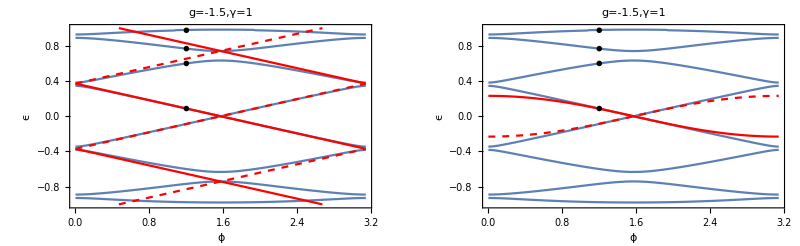

```mathematica
Clear["Global`*","SubPlus","SubMinus","Subscript"];
Nn=2;branchesΞ1st=Flatten@Table[fΞ1st[ϕ,n,τ],{n,-Nn,Nn-1,1},{τ,{+1,-1}}];branchesΞ2ed=Table[fΞ2ed[ϕ,τ],{τ,{+1,-1}}];
fΞ1st[ϕ_,n_,τ_]:=(2J)/t*2 √Ω(π/2-τ ϕ+n π) /(L/(t a)+((γ-λ)^2+2 Ω)/(2 γ Ω));
fΞ2ed[ϕ_,τ_]:=(2J)/t*((τ 2Ω Cos[ϕ])/(√(1+((a t+L γ)^2 Ω)/(a^2 t^2 γ^2)+3 Cos[ϕ]^2-2ζ+((γ^2 (-1+ζ)^4)/(4Ω)+ζ^2)Sin[(L √Ω)/(a t)-ArcTan[(2 ζ √Ω)/(γ (-1+ζ)^2)]]^2+(L γ (-1+ζ)^2)/(a t) )));
fΞ[ϕ_]:=(Clear[ϵ];
DeleteCases[Union[Abs[ϵ/.FindRoot[Re[Subscript[𝒮, 0]^2 ⅇ^(ⅈ (SubPlus[KN]-SubMinus[KN])L)- Subscript[𝒮, 1]^2 ⅇ^(ⅈ (SubPlus[KN]+SubMinus[KN])L)]==Subscript[𝒮, 2]^2 Cos[2 ϕ],{ϵ,#}]&/@RandomReal[{0,ℱGap[J,t,γ,g]},50]],SameTest->(Abs[#1-#2]<0.001&)],sol_/;sol>ℱGap[J,t,γ,g]-0.001]);

J=1;a=1;t=1;γ=1;L=10;λ=0;g=-1.5;ϕ0=1.2;
Ξ=t ϵ/(2J);Γ=2 γ^2;Ω=t(2t+g);Λ=√(Γ^2+Ξ^2-2Γ Ω);
U=ArcCos[(Λ-Ξ)/Γ]/2;V=ArcCos[(Λ+Ξ)/Γ]/2;α=U+V;β=U-V;ζ=λ/γ ;
SubPlus[KS]=2 γ Cos[U] Cos[V]/(t a);SubMinus[KS]=2 γ Sin[U] Sin[V]/(t a);SubPlus[KN]=2 γ Sin[U]Cos[V]/(t a);SubMinus[KN]=2 γ  Cos[U]Sin[V]/(t a);
Subscript[𝒮, 0]=Sin[β](1+ζ^2-2ζ ⅇ^(+ⅈ β))-2 ⅈ ⅇ^(+ⅈ β) (Sin[α]^2-Sin[β]^2);Subscript[𝒮, 1]=-Sin[β](1+ζ^2-2 ζ (Cos[β]+ⅈ Sin[α]));Subscript[𝒮, 2]=2 Sin[α] √(Sin[α]^2-Sin[β]^2);
listΞ=fΞ[ϕ0];
criticalContour=ContourPlot[Re[Subscript[𝒮, 0]^2 ⅇ^(ⅈ (SubPlus[KN]-SubMinus[KN])L)- Subscript[𝒮, 1]^2 ⅇ^(ⅈ (SubPlus[KN]+SubMinus[KN])L)]==Subscript[𝒮, 2]^2 Cos[2 ϕ],{ϕ,0,Pi},{ϵ,-ℱGap[J,t,γ,g],ℱGap[J,t,γ,g]},Exclusions->{ϵ==-ℱGap[J,t,γ,g],ϵ==ℱGap[J,t,γ,g]},Epilog->{PointSize[0.01],Black,Evaluate@Point[{ϕ0,#}&/@listΞ]},AspectRatio->Automatic,ContourShading->None,ContourLabels->None,FrameLabel->{"ϕ","ϵ"},PlotLabel->"g="<>ToString[g]<>",γ="<>ToString[γ],BaseStyle->{FontSize->14},PlotPoints->50];

{criticalPlot1st,criticalPlot2st}=Plot[#,{ϕ,0,Pi},PlotRange->{Automatic,{-ℱGap[J,t,γ,g],ℱGap[J,t,γ,g]}},PlotStyle->{Red,{Red,Dashed}}]&/@{branchesΞ1st,branchesΞ2ed};

GraphicsGrid[{{Show[criticalContour,criticalPlot1st],Show[criticalContour,criticalPlot2st]}},ImageSize->Full]
```

## Full Normalized Wavefunction Plots

```mathematica
Clear["Global`*","SubPlus","SubMinus","Subscript"];
fΞ[ϕ_]:=(Clear[ϵ];
DeleteCases[Union[Abs[ϵ/.FindRoot[Re[Subscript[𝒮, 0]^2 ⅇ^(ⅈ (SubPlus[KN]-SubMinus[KN])L)- Subscript[𝒮, 1]^2 ⅇ^(ⅈ (SubPlus[KN]+SubMinus[KN])L)]==Subscript[𝒮, 2]^2 Cos[2 ϕ],{ϵ,#}]&/@RandomReal[{0,ℱGap[J,t,γ,g]},50]],SameTest->(Abs[#1-#2]<0.001&)],sol_/;sol>ℱGap[J,t,γ,g]-0.001]);
uL[x_]:=+C1*Cos[U]*Exp[+SubPlus[KS]x]+C2*Sin[V]*Exp[+SubMinus[KS]x];
vL[x_]:=-C1*Cos[V]*Exp[+SubPlus[KS]x]-C2*Sin[U]*Exp[+SubMinus[KS]x];
uM[x_]:=+C5*Exp[+ⅈ SubPlus[KN] x]+C6*Exp[-ⅈ SubPlus[KN] x];
vM[x_]:=+C7*Exp[+ⅈ SubMinus[KN] x]+C8*Exp[-ⅈ SubMinus[KN] x];
uR[x_]:=ⅇ^(-ⅈ ϕ)(C3*Cos[U]*Exp[-SubPlus[KS]x]+C4*Sin[V]*Exp[-SubMinus[KS]x]);
vR[x_]:=ⅇ^(+ⅈ ϕ)(C3*Cos[V]*Exp[-SubPlus[KS]x]+C4*Sin[U]*Exp[-SubMinus[KS]x]);
NormSqureCritical[WF_]:=Simplify[((WF/.{Complex[a_,b_]:>Complex[a,-b]})*WF)]
NCriticalU[x_]:=Which[x≤-L/2,uL[x],-L/2<x<L/2,uM[x],x≥L/2,uR[x]]
NCriticalV[x_]:=Which[x≤-L/2,vL[x],-L/2<x<L/2,vM[x],x≥L/2,vR[x]]
NCriticalU2PV2[x_]:=NormSqureCritical[NCriticalU[x]]+NormSqureCritical[NCriticalV[x]];
NCriticalU2MV2[x_]:=NormSqureCritical[NCriticalU[x]]-NormSqureCritical[NCriticalV[x]];
Cuv={C1,C2,C3,C4,C5,C6,C7,C8};x0=0;xL=x0-L/2;xR=x0+L/2;
Buv={uL[xL]==uM[xL],vL[xL]==vM[xL],uR[xR]==uM[xR],vR[xR]==vM[xR],
(t*a*uL'[xL]+γ*vL[xL])==(t*a*uM'[xL]+λ*uM[xL]),(t*a*vL'[xL]+γ*uL[xL])==(t*a*vM'[xL]+λ*vM[xL]),
(t*a*uR'[xR]+γ*ⅇ^(-2ⅈ ϕ)*vR[xR])==(t*a*uM'[xR]-λ*uM[xR]),(t*a*vR'[xR]+γ*ⅇ^(+2ⅈ ϕ)*uR[xR])==(t*a*vM'[xR]-λ*vM[xR])};
Duv={t*a^2*uL''[x]+2γ*a*vL'[x]+(2t+g+ϵ/(2J))*uL[x],t*a^2*vL''[x]+2γ*a*uL'[x]+(2t+g-ϵ/(2J))*vL[x],
t*a^2*uM''[x]+(2t+g+ϵ/(2J))*uM[x],t*a^2*vM''[x]+(2t+g-ϵ/(2J))*vM[x],
t*a^2*uR''[x]+2γ*a*ⅇ^(-2ⅈ ϕ)*vR'[x]+(2t+g+ϵ/(2J))*uR[x],t*a^2*vR''[x]+2γ*a*ⅇ^(+2ⅈ ϕ)*uR'[x]+(2t+g-ϵ/(2J))*vR[x]};

J=1;a=1;t=1;γ=1;L=10;λ=0;g=-1.5;ϕ0=2.2;
U=ArcCos[(Λ-Ξ)/Γ]/2;V=ArcCos[(Λ+Ξ)/Γ]/2;α=U+V;β=U-V;ζ=λ/γ ;
SubPlus[KS]=2 γ Cos[U] Cos[V]/(t a);SubMinus[KS]=2 γ Sin[U] Sin[V]/(t a);SubPlus[KN]=2 γ Sin[U]Cos[V]/(t a);SubMinus[KN]=2 γ  Cos[U]Sin[V]/(t a);
Subscript[𝒮, 0]=Sin[β](1+ζ^2-2ζ ⅇ^(+ⅈ β))-2 ⅈ ⅇ^(+ⅈ β) (Sin[α]^2-Sin[β]^2);Subscript[𝒮, 1]=-Sin[β](1+ζ^2-2 ζ (Cos[β]+ⅈ Sin[α]));Subscript[𝒮, 2]=2 Sin[α] √(Sin[α]^2-Sin[β]^2);
Ξ=t ϵ/(2J);Γ=2 γ^2;Ω=t(2t+g);Λ=√(Γ^2+Ξ^2-2Γ Ω);
listΞ=fΞ[ϕ0]
```

{0.147934,0.556161,0.799482,0.969067}

Solve::svars: 方程可能无法给出所有 " solve " 变量的解.

{{True,True,True,True,True,True,True,True},1.,{0,0,0,0,0,0}}

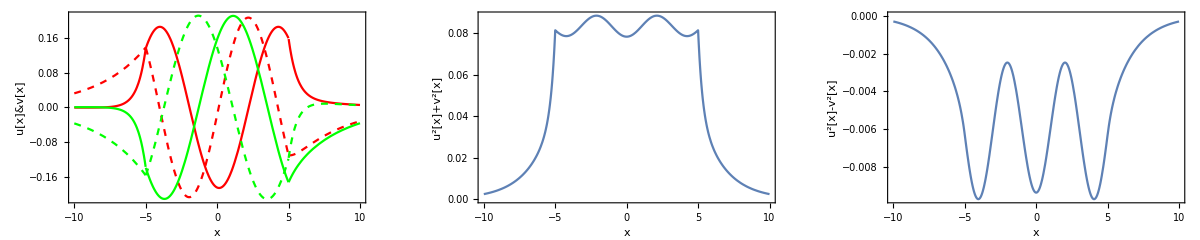

```mathematica
Clear[C1,C2,C3,C4,C5,C6,C7,C8]
ϕ=ϕ0;ϵ=listΞ[[1]];
{C1,C2,C3,C4,C5,C6,C7,C8}=Flatten[Cuv/.Chop[Solve[Buv[[1;;7]],Cuv]]];
C1=Sqrt[1/Chop[NIntegrate[Coefficient[Total@NormSqureCritical[{uL[x],vL[x]}],C1^2],{x,-∞,-L/2}]+NIntegrate[Coefficient[Total@NormSqureCritical[{uM[x],vM[x]}],C1^2],{x,-L/2,+L/2}]+NIntegrate[Coefficient[Total@NormSqureCritical[{uR[x],vR[x]}],C1^2],{x,+L/2,+∞}]]];
{Buv,NIntegrate[Total@NormSqureCritical[{uL[x],vL[x]}],{x,-∞,-L/2}]+
NIntegrate[Total@NormSqureCritical[{uM[x],vM[x]}],{x,-L/2,L/2}]+
NIntegrate[Total@NormSqureCritical[{uR[x],vR[x]}],{x,L/2,∞}],Duv}//Simplify//Chop
GraphicsRow[{Plot[{Re@NCriticalU[x],Im@NCriticalU[x],Re@NCriticalV[x],Im@NCriticalV[x]},{x,-L,L},PlotStyle->{Red,{Red,Dashed},Green,{Green,Dashed}},(*PlotLegends->{"Re@u[x]","Im@u[x]","Re@v[x]","Im@v[x]"},*)Frame->True,FrameLabel->{"x","u[x]&v[x]"}],
Plot[NCriticalU2PV2[x],{x,-L,L},Frame->True,FrameLabel->{"x","u^2[x]+v^2[x]"}],
Plot[NCriticalU2MV2[x],{x,-L,L},Frame->True,FrameLabel->{"x","u^2[x]-v^2[x]"}]},ImageSize->Full]
```

## Wavefunctions in Deep Topological

## Expressions

### General

```mathematica
Clear["Global`*","SubPlus","SubMinus","Subscript"];
u[x_]:=ⅇ^(-ⅈ ϕ)(C1*Exp[-ⅈ W]*Exp[+τ Κ x]+C2*Exp[+ⅈ W]*Exp[-τ Κ x]);
v[x_]:=ⅇ^(+ⅈ ϕ)(C1*Exp[+ⅈ W]*Exp[+τ Κ x]+C2*Exp[-ⅈ W]*Exp[-τ Κ x]);
kF=ArcCos[-g/(2t)]/a;Υ=2t a Sin[kF a];Δ=2γ Sin[kF a];Ε=ϵ/(2J);
Κ=√(Δ^2-Ε^2)/Υ;W=ArcCos[Ε/Δ]/2;
ruleNM={J->1.1,a->0.9,t->1.1,γ->0.3,g->-0.3,ϵ->0.1,ϕ->7,τ->+1};
Chop@Simplify[{
-τ ⅈ*Υ*u'[x]+Δ*ⅇ^(-2ⅈ ϕ)*v[x]-Ε*u[x],
+τ ⅈ*Υ*v'[x]+Δ*ⅇ^(+2ⅈ ϕ)*u[x]-Ε*v[x]}/.ruleNM//N]
```

{0,0}

### Left-Middle-Right

```mathematica
Clear["Global`*","SubPlus","SubMinus","Subscript"];
uL[x_]:=C1*Exp[-ⅈ τ W]*Exp[+KS x];vL[x_]:=C1*Exp[+ⅈ τ W]*Exp[+KS x];
uM[x_]:=C3*Exp[+ⅈ τ KN x];vM[x_]:=C4*Exp[-ⅈ τ KN x];
uR[x_]:=ⅇ^(-ⅈ ϕ)(C2*Exp[+ⅈ τ W]*Exp[-KS x]);vR[x_]:=ⅇ^(+ⅈ ϕ)(C2*Exp[-ⅈ τ W]*Exp[-KS x]);
kF=ArcCos[-g/(2t)]/a;Υ=2t a Sin[kF a];Δ=2γ Sin[kF a];Ε=ϵ/(2J);
KS=√(Δ^2-Ε^2)/Υ;KN = Ε/Υ;W=ArcCos[Ε/Δ]/2;
ruleNM={J->1.1,a->0.9,t->1.1,γ->0.3,g->-0.3,ϵ->0.1,ϕ->7,τ->+1};
Simplify[{
-τ ⅈ*Υ*uL'[x]+Δ*vL[x]-Ε*uL[x],
+τ ⅈ*Υ*vL'[x]+Δ*uL[x]-Ε*vL[x],
-τ ⅈ*Υ*uR'[x]+Δ*ⅇ^(-2ⅈ ϕ)*vR[x]-Ε*uR[x],
+τ ⅈ*Υ*vR'[x]+Δ*ⅇ^(+2ⅈ ϕ)*uR[x]-Ε*vR[x]}/.ruleNM//N]//Chop
```

{0,0,0,0}

## Scattering Matrices

### Right Junction

```mathematica
(*+1 for electron*)
Clear["Global`*","SubPlus","SubMinus","Subscript"];SR0={{0,0},{0,0}};
uM[x_]:=+IE*Exp[+ⅈ KN x];vM[x_]:=+RH*Exp[-ⅈ KN x];
uR[x_]:=ⅇ^(-ⅈ ϕ)(C1*Exp[+ⅈ W]*Exp[-KS x]);vR[x_]:=ⅇ^(+ⅈ ϕ)(C1*Exp[-ⅈ W]*Exp[-KS x]);
x0=0;Cuv={RE,RH,C1};Buv={uR[x0]==uM[x0],vR[x0]==vM[x0]};sol=Solve[Buv,Cuv];
SR0[[2,1]]=Coefficient[Flatten[sol/.Rule->List][[2]],IE];
(*-1 for hole*)
uM[x_]:=+RE*Exp[-ⅈ KN x];vM[x_]:=+IH*Exp[+ⅈ KN x];
uR[x_]:=ⅇ^(-ⅈ ϕ)(C1*Exp[-ⅈ W]*Exp[-KS x]);vR[x_]:=ⅇ^(+ⅈ ϕ)(C1*Exp[+ⅈ W]*Exp[-KS x]);
x0=0;Cuv={RE,RH,C1};Buv={uR[x0]==uM[x0],vR[x0]==vM[x0]};sol=Solve[Buv,Cuv];
SR0[[1,2]]=Coefficient[Flatten[sol/.Rule->List][[2]],IH];

SR=ⅇ^(-2 ⅈ W)MatrixExp[-2 ⅈ ϕ ρZ].ρX;
MatrixForm[#]&/@{SR0,(SR0/.{W->-W}).SR0,SR0==SR}
```

Solve::svars: 方程可能无法给出所有 " solve " 变量的解.

{(0 | ⅇ^(-2 ⅈ W-2 ⅈ ϕ)
ⅇ^(-2 ⅈ W+2 ⅈ ϕ) | 0),(1 | 0
0 | 1),True}

### Left Junction

```mathematica
(*-1 for electron*)
Clear["Global`*","SubPlus","SubMinus","Subscript"];SL0={{0,0},{0,0}};
uM[x_]:=+IE*Exp[-ⅈ KN x];vM[x_]:=+RH*Exp[+ⅈ KN x];
uL[x_]:=C1*Exp[+ⅈ W]*Exp[+KS x];vL[x_]:=C1*Exp[-ⅈ W]*Exp[+KS x];
x0=0;Cuv={RE,RH,C1};Buv={uL[x0]==uM[x0],vL[x0]==vM[x0]};sol=Solve[Buv,Cuv];
SL0[[2,1]]=Coefficient[Flatten[sol/.Rule->List][[2]],IE];
(*+1 for hole*)
uM[x_]:=+RE*Exp[+ⅈ KN x];vM[x_]:=+IH*Exp[-ⅈ KN x];
uL[x_]:=C1*Exp[-ⅈ W]*Exp[+KS x];vL[x_]:=C1*Exp[+ⅈ W]*Exp[+KS x];
x0=0;Cuv={RE,RH,C1};Buv={uL[x0]==uM[x0],vL[x0]==vM[x0]};sol=Solve[Buv,Cuv];
SL0[[1,2]]=Coefficient[Flatten[sol/.Rule->List][[2]],IH];

SL=ⅇ^(-2 ⅈ W)ρX;
MatrixForm[#]&/@{SL0,(SL0/.{W->-W}).SL0,SL0==SL}
```

Solve::svars: 方程可能无法给出所有 " solve " 变量的解.

{(0 | ⅇ^(-2 ⅈ W)
ⅇ^(-2 ⅈ W) | 0),(1 | 0
0 | 1),True}

Universal Expression by redefining UV with τ_z

```mathematica
Clear["Global`*","SubPlus","SubMinus","Subscript"];
uL[x_]:=C1*V*Exp[+KS x];vL[x_]:=C1*U*Exp[+KS x];
uM[x_]:=C3*Exp[+ⅈ τ KN x];vM[x_]:=C4*Exp[-ⅈ τ KN x];
uR[x_]:=ⅇ^(-ⅈ ϕ)C2*U*Exp[-KS x];vR[x_]:=ⅇ^(+ⅈ ϕ)C2*V*Exp[-KS x];
Ε=ϵ/(2J);kF=ArcCos[-g/(2t)]/a;Υ=2t a Sin[kF a];Δ=2γ Sin[kF a];
KS=√(Δ^2-Ε^2)/Υ;KN = Ε/Υ;U=√(Ε+ⅈ Subscript[τ, z] Υ KS);V=√(Ε-ⅈ Subscript[τ, z] Υ KS);
ruletest={J->1.1,a->0.9,t->1.1,γ->0.3,g->-0.3,ϵ->0.1,ϕ->7,Subscript[τ, z]->+1};
Simplify[{
-Subscript[τ, z]ⅈ*Υ*uL'[x]+Δ*vL[x]-Ε*uL[x],
+Subscript[τ, z]ⅈ*Υ*vL'[x]+Δ*uL[x]-Ε*vL[x],
-Subscript[τ, z]ⅈ*Υ*uR'[x]+Δ*ⅇ^(-2ⅈ ϕ)*vR[x]-Ε*uR[x],
+Subscript[τ, z]ⅈ*Υ*vR'[x]+Δ*ⅇ^(+2ⅈ ϕ)*uR[x]-Ε*vR[x]}/.ruletest//N]//Chop
```

{0,0,0,0}

### DET

```mathematica
Clear["Global`*","SubPlus","SubMinus","Subscript"];
SL=ⅇ^(-2 ⅈ W)ρX;SM=ⅇ^(ⅈ KN L)MatrixExp[ⅈ ρZ kF];SR=ⅇ^(-2 ⅈ W)MatrixExp[-2 ⅈ ϕ ρZ].ρX;
DET0=FullSimplify[Det[ρI-SM.SR.SM.SL]]
```

1+ⅇ^(4 ⅈ (KN L-2. W))-ⅇ^(2 ⅈ (KN L-2. W-1. ϕ))-ⅇ^(2 ⅈ (KN L-2. W+ϕ))

```mathematica
(*Simplify by W=ArcCos[Ε/Δ]/2,KN = Ε/Υ*)
L Ε/Υ+τ ϕ==ArcCos[Ε/Δ]+n π;
```

## Spectrum ContourPlot

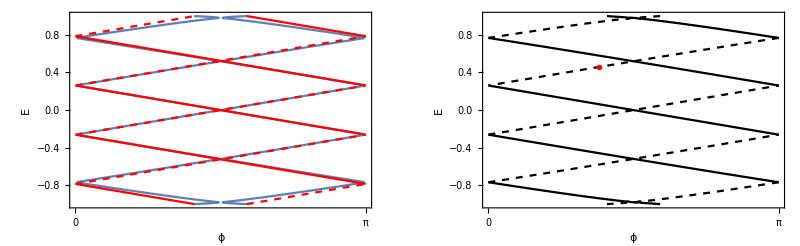

```mathematica
Clear["Global`*","SubPlus","SubMinus","Subscript"];
Nn=3;branchesΕ=Flatten@Table[fΕDET[ϕ,n,τ],{n,-Nn,Nn-1,1},{τ,{+1,-1}}];branchesΕ1st=Flatten@Table[fΕ1st[ϕ,n,τ],{n,-Nn,Nn-1,1},{τ,{+1,-1}}];
fΕ[ϕ_,n_,τ_]:=Chop@FindRoot[L Ε/Υ+τ ϕ==ArcCos[Ε/Δ]+n π,{Ε,0}][[1,2]];fΕDET[ϕ_,n_,τ_]:=L Ε/Υ+τ ϕ-(ArcCos[Ε/Δ]+n π);fΕ1st[ϕ_,n_,τ_]:=(π/2-τ ϕ+n π)/(L/Υ+1/Δ);
J=1;a=1;t=1;γ=0.5;g=-0.;L=10;Nn=2;ϕ0=1.2;n0=0;τ0=-1;
KN = Ε/Υ;kF=ArcCos[-g/(2t)]/a;Υ=2t a Sin[kF a];Δ=2γ Sin[kF a];W=ArcCos[Ε/Δ]/2;
deepContour1=ContourPlot[Cos[2 KN L-4 W]==Cos[2 ϕ],{ϕ,0,Pi},{Ε,-Δ,Δ},AspectRatio->Automatic,ContourShading->None,ContourLabels->None,FrameLabel->{"ϕ","Ε"},FrameTicks->{{Automatic,None},{{0,Pi},None}},BaseStyle->{FontFamily->"Times",FontSize->10},PlotPoints->25];
deepContour2=ContourPlot[branchesΕ,{ϕ,0,Pi},{Ε,-Δ,Δ},Epilog->{PointSize[0.01],Red,Evaluate@Point[{ϕ0,fΕ[ϕ0,n0,τ0]}]},AspectRatio->Automatic,ContourShading->None,ContourLabels->None,FrameLabel->{"ϕ","Ε"},FrameTicks->{{Automatic,None},{{0,Pi},None}},ContourStyle->{Black,{Dashed,Black}},BaseStyle->{FontFamily->"Times",FontSize->10},PlotPoints->25];
deepPlot1st=Plot[branchesΕ1st,{ϕ,0,Pi},PlotRange->{Automatic,{-Δ,Δ}},PlotStyle->{Red,{Red,Dashed}}];
GraphicsGrid[{{Show[deepContour1,deepPlot1st],deepContour2}},ImageSize->Full]
```

## Full Normalized Wavefunction Plots

{0.611011,1.}

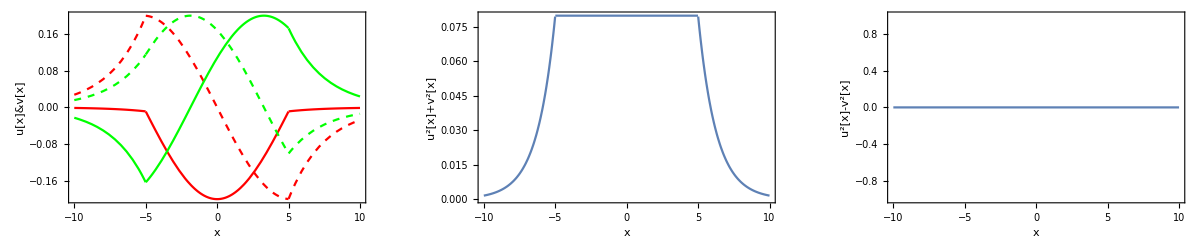

```mathematica
Clear["Global`*","SubPlus","SubMinus","Subscript"];
(*Full Normalized Wave Functions*)
fΕ[ϕ_,n_,τ_]:=Chop@FindRoot[Nm Ε/Υ+τ ϕ==ArcCos[Ε/Δ]+n π,{Ε,0}][[1,2]];
NormSqureNumerics[WF_]:=Simplify[((WF/.{Complex[a_,b_]:>Complex[a,-b]})*WF)];
fl[x_]:=Which[x≤-Nm/2,-Nm/2,-Nm/2<x<+Nm/2,x,x≥+Nm/2,+Nm/2];
DeepU[x_]:=A*(-1)^n Exp[-KS Abs[x-fl[x]]]*Exp[+ⅈ τ KN fl[x]];
DeepV[x_]:=A*ⅇ^(+ⅈ ϕ)*Exp[-KS Abs[x-fl[x]]]*Exp[-ⅈ τ KN fl[x]];
DeepU2PV2[x_]:=NormSqureNumerics[DeepU[x]]+NormSqureNumerics[DeepV[x]];
DeepU2MV2[x_]:=NormSqureNumerics[DeepU[x]]-NormSqureNumerics[DeepV[x]];
(*Constant Definitions*)
A=1/√(2 (Nm+1/KS));KS=√(Δ^2-Ε^2)/Υ;KN = Ε/Υ;kF=ArcCos[-g/(2t)]/a;Υ=2t a Sin[kF a];Δ=2γ Sin[kF a];
(*Numerics*)
J=1;a=1;t=1;γ=0.5;g=-0.;Nm=10;x0=0;{Ε=fΕ[ϕ=1.,n=1,τ=+1],NIntegrate[DeepU2PV2[x],{x,-∞,+∞}]}
deepPlotUV=Plot[{Re@DeepU[x],Im@DeepU[x],Re@DeepV[x],Im@DeepV[x]},{x,-Nm,Nm},PlotStyle->{Red,{Red,Dashed},Green,{Green,Dashed}},Frame->True,FrameLabel->{"x","u[x]&v[x]"}];
deepPlotU2PV2=Plot[DeepU2PV2[x],{x,-Nm,Nm},Frame->True,FrameLabel->{"x","u^2[x]+v^2[x]"}];
deepPlotU2MV2=Plot[Chop@DeepU2MV2[x],{x,-Nm,Nm},Frame->True,FrameLabel->{"x","u^2[x]-v^2[x]"}];
GraphicsRow[{deepPlotUV,deepPlotU2PV2,deepPlotU2MV2},ImageSize->Full]
```

## Entanglement

```mathematica
Clear["Global`*"];
<<Wolfram`QuantumFramework`
express={QuantumEntanglementMonotone[QuantumState[{α,0,0,Sqrt[1-α^2]}],{{1},{2}},"Concurrence"], QuantumEntanglementMonotone[QuantumState[{α,0,0,Sqrt[1-α^2]}],{{1},{2}},"LogNegativity"],QuantumEntanglementMonotone[QuantumState[{α,0,0,Sqrt[1-α^2]}],{{1},{2}},"EntanglementEntropy"]};
```

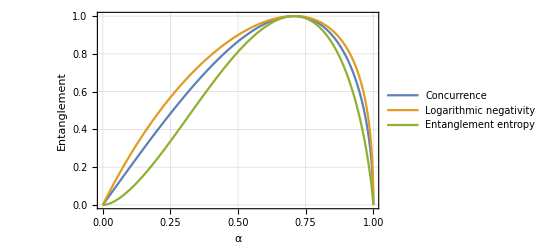

```mathematica
Plot[express,{α,0,1},FrameLabel->{"α","Entanglement"},PlotLegends->Placed[{"Concurrence","Logarithmic negativity","Entanglement entropy"},{0.65,0.4}],PlotTheme->"Detailed",LabelStyle->{Black,14,FontFamily->"Times"},ImageSize->400]
```

# Appendix The Honeycomb Ising Model

## Brute Force

```mathematica
Clear["Global`*"];m=2;n=3;Ν=4m n;
μ[2m+1,x_]:=μ[1,x];μ[x_,2n+1]:=μ[x,1];(*PBC*)
singleH=Sum[
K1*μ[2i-1,2j-1]*μ[2i,2j-1]+K2*μ[2i-1,2j]*μ[2i,2j]+K3*μ[2i,2j]*μ[2i,2j+1]+
K2*μ[2i,2j-1]*μ[2i+1,2j-1]+K1*μ[2i,2j]*μ[2i+1,2j]+K3*μ[2i+1,2j-1]*μ[2i+1,2j],{i,1,m},{j,1,n}];
siteIndex=Flatten@Table[μ[i,j],{i,1,2m},{j,1,2n}];
singleConf[conf_]:=Exp[singleH/.Thread[siteIndex->conf]];
{K1,K2,K3}=(SeedRandom[0608];RandomReal[{0,0.1},3]);
Total@ParallelMap[singleConf,Tuples[{-1.,1.},Ν]]
```

1.72496×10^7

## Transfer Matrix Construction

## Original Matrix

```mathematica
Clear["Global`*"];m=2;n=3;Ν=4m n;
𝕦[2n+1]:=𝕦[1];μ[2n+1]:=μ[1];(*PBC*)
μIndex=Table[μ[j],{j,1,2n}];𝕦Index=Table[𝕦[j],{j,1,2n}];
{K1,K2,K3}=(SeedRandom[0608];RandomReal[{0,0.1},3]);
pa[μConf_,𝕦Conf_]:=∏_(j=1)^n Exp[K1*μ[2j-1]*𝕦[2j-1]+K2*μ[2j]*𝕦[2j]+K3*𝕦[2j]*𝕦[2j+1]]/.Thread[μIndex->μConf]/.Thread[𝕦Index->𝕦Conf];
pb[μConf_,𝕦Conf_]:=∏_(j=1)^n Exp[K2*μ[2j-1]*𝕦[2j-1]+K1*μ[2j]*𝕦[2j]+K3*𝕦[2j-1]*𝕦[2j]]/.Thread[μIndex->μConf]/.Thread[𝕦Index->𝕦Conf];
Pa=Table[pa[μConf,𝕦Conf],{μConf,Tuples[{1,-1},2n]},{𝕦Conf,Tuples[{1,-1},2n]}];
Pb=Table[pb[μConf,𝕦Conf],{μConf,Tuples[{1,-1},2n]},{𝕦Conf,Tuples[{1,-1},2n]}];P=Pa.Pb;
Tr@MatrixPower[P,m]
```

1.72496×10^7

## Matrix Decomposition

```mathematica
v1x[μConf_,𝕦Conf_]:=∏_(j=1)^n Exp[K1*μ[2j-1]*𝕦[2j-1]+K2*μ[2j]*𝕦[2j]]/.Thread[μIndex->μConf]/.Thread[𝕦Index->𝕦Conf];
v2[μConf_,𝕦Conf_]:=∏_(j=1)^n Exp[K3*𝕦[2j]*𝕦[2j+1]]∏_(j=1)^(2n) μ[j],𝕦[j]/.Thread[μIndex->μConf]/.Thread[𝕦Index->𝕦Conf];
v3x[μConf_,𝕦Conf_]:=∏_(j=1)^n Exp[K2*μ[2j-1]*𝕦[2j-1]+K1*μ[2j]*𝕦[2j]]/.Thread[μIndex->μConf]/.Thread[𝕦Index->𝕦Conf];
v4[μConf_,𝕦Conf_]:=∏_(j=1)^n Exp[K3*𝕦[2j-1]*𝕦[2j]]∏_(j=1)^(2n) μ[j],𝕦[j]/.Thread[μIndex->μConf]/.Thread[𝕦Index->𝕦Conf];
{V1x,V2,V3x,V4}=Table[#[μConf,𝕦Conf],{μConf,Tuples[{1,-1},2n]},{𝕦Conf,Tuples[{1,-1},2n]}]&/@{v1x,v2,v3x,v4};
P==V1x.V2.V3x.V4
```

True

## Pauli Representation

```mathematica
x_≈y_:=Chop[x-y]==Table[0,2^(2n),2^(2n)];
ss[x_,2n+1]:=ss[x,1];(*PBC*)
c[i_]:=KroneckerProduct@@ReplacePart[Table[σI,2n],i->σX];
ss[i_,j_]:=KroneckerProduct@@ReplacePart[Table[σI,2n],{i->σZ,j->σZ}];
𝕍1=MatrixExp[K1S*Sum[c[i],{i,1,2n-1,2}]+K2S*Sum[c[i],{i,2,2n,2}]];
𝕍2=MatrixExp[K3*Sum[ss[i,i+1],{i,2,2n,2}]];
𝕍3=MatrixExp[K2S*Sum[c[i],{i,1,2n-1,2}]+K1S*Sum[c[i],{i,2,2n,2}]];
𝕍4=MatrixExp[K3*Sum[ss[i,i+1],{i,1,2n-1,2}]];
ℙ=(2Sinh[2 K1])^n(2Sinh[2 K2])^n 𝕍1.𝕍2.𝕍3.𝕍4;
K1S=Log@Coth[K1]/2;K2S=Log@Coth[K2]/2;{σI,σX,σY,σZ}=PauliMatrix[{0,1,2,3}];
{(2Sinh[2K1])^(n/2)(2Sinh[2K2])^(n/2)𝕍1≈V1x,𝕍2≈V2,(2Sinh[2K1])^(n/2)(2Sinh[2K2])^(n/2)𝕍3≈V3x,𝕍4≈V4,ℙ≈P}
```

{True,True,True,True,True}

## Γ Representation

```mathematica
Clear[𝕍1,𝕍2,𝕍3,𝕍4]
{σI,σX,σY,σZ}=PauliMatrix[{0,1,2,3}];𝟙=IdentityMatrix[2^(2n)];{K1★,K2★,K3★}=1/2Log@*Coth/@{K1,K2,K3};
γ[i_]:=If[OddQ[i],Join[Table[σX,Ceiling[i/2]-1],{σZ},Table[σI,2n-Ceiling[i/2]]],Join[Table[σX,Ceiling[i/2]-1],{-σY},Table[σI,2n-Ceiling[i/2]]]];
Γ=KroneckerProduct@@@Array[γ,4n];𝕌=KroneckerProduct@@Table[σX,2n];
𝕍1=MatrixExp[K1★*Sum[-ⅈ Γ[[2j-1]].Γ[[2j]],{j,1,2n-1,2}]+K2★*Sum[-ⅈ Γ[[2j-1]].Γ[[2j]],{j,2,2n,2}]];
𝕍2[x_]:=MatrixExp[K3*Sum[-ⅈ Γ[[2j]].Γ[[2j+1]],{j,2,2n-1,2}]].MatrixExp[K3*(ⅈ x. Γ[[4n]]. Γ[[1]])];
𝕍3=MatrixExp[K2★*Sum[-ⅈ Γ[[2j-1]].Γ[[2j]],{j,1,2n-1,2}]+K1★*Sum[-ⅈ Γ[[2j-1]].Γ[[2j]],{j,2,2n,2}]];
𝕍4=MatrixExp[K3*Sum[-ⅈ Γ[[2j]].Γ[[2j+1]],{j,1,2n-1,2}]];𝕍[x_]:=𝕍1.𝕍2[x].𝕍3.𝕍4;
Chop@Tr@MatrixPower[(2Sinh[2 K1])^n(2Sinh[2 K2])^n 𝕍[𝕌],m]
```

1.72496×10^7

```mathematica
ss[x_,2n+1]:=ss[x,1];(*PBC*)
c[i_]:=KroneckerProduct@@ReplacePart[Table[σI,2n],i->σX];
ss[i_,j_]:=KroneckerProduct@@ReplacePart[Table[σI,2n],{i->σZ,j->σZ}];
{𝕌==ⅈ^(2n)Dot@@Γ,ss[2n,2n+1]==ⅈ 𝕌. Γ[[4n]]. Γ[[1]],
Array[c,2n]==Table[-ⅈ Γ[[2j-1]].Γ[[2j]],{j,1,2n}],
Array[ss[#,#+1]&,2n-1]==Table[-ⅈ Γ[[2j]].Γ[[2j+1]],{j,1,2n-1}],𝕍1==MatrixExp[K1★*Sum[c[i],{i,1,2n-1,2}]+K2★*Sum[c[i],{i,2,2n,2}]],
𝕍2[𝕌]==MatrixExp[K3*Sum[ss[i,i+1],{i,2,2n,2}]],
𝕍3==MatrixExp[K2★*Sum[c[i],{i,1,2n-1,2}]+K1★*Sum[c[i],{i,2,2n,2}]],
𝕍4==MatrixExp[K3*Sum[ss[i,i+1],{i,1,2n-1,2}]]}
```

{True,True,True,True,True,True,True,True}

```mathematica
S[θ_,μ_,ν_]:=MatrixExp[θ/2 Γ[[μ]].Γ[[ν]]];
{𝕍1==Dot@@Table[S[-2ⅈ K1★,2j-1,2j],{j,1,2n-1,2}].Dot@@Table[S[-2ⅈ K2★,2j-1,2j],{j,2,2n,2}],
𝕍2[+𝟙]==Dot@@Table[S[-2ⅈ K3,2j,2j+1],{j,2,2n-1,2}].S[+2ⅈ K3,4n,1],
𝕍2[-𝟙]==Dot@@Table[S[-2ⅈ K3,2j,2j+1],{j,2,2n-1,2}].S[-2ⅈ K3,4n,1],𝕍3==Dot@@Table[S[-2ⅈ K2★,2j-1,2j],{j,1,2n-1,2}].Dot@@Table[S[-2ⅈ K1★,2j-1,2j],{j,2,2n,2}],𝕍4==Dot@@Table[S[-2ⅈ K3,2j,2j+1],{j,1,2n-1,2}]}
```

{True,True,True,False,True}

## S Representation

```mathematica
{σI,σX,σY,σZ}=PauliMatrix[{0,1,2,3}];𝟙=IdentityMatrix[2^(2n)];{K1★,K2★,K3★}=1/2Log@*Coth/@{K1,K2,K3};
S[θ_,μ_,ν_]:=MatrixExp[θ/2 Γ[[μ]].Γ[[ν]]];x_≈y_:=Chop[x-y]==Table[0,2^(2n),2^(2n)];
γ[i_]:=If[OddQ[i],Join[Table[σX,Ceiling[i/2]-1],{σZ},Table[σI,2n-Ceiling[i/2]]],Join[Table[σX,Ceiling[i/2]-1],{-σY},Table[σI,2n-Ceiling[i/2]]]];
Γ=KroneckerProduct@@@Array[γ,4n];𝕌=KroneckerProduct@@Table[σX,2n];
𝒱1=Dot@@Table[S[-2ⅈ K1★,2j-1,2j],{j,1,2n-1,2}].Dot@@Table[S[-2ⅈ K2★,2j-1,2j],{j,2,2n,2}];
𝒱2[x_]:=Dot@@Table[S[-2ⅈ K3,2j,2j+1],{j,2,2n-1,2}].S[+x 2ⅈ K3,4n,1];𝒱3=Dot@@Table[S[-2ⅈ K2★,2j-1,2j],{j,1,2n-1,2}].Dot@@Table[S[-2ⅈ K1★,2j-1,2j],{j,2,2n,2}];
𝒱4=Dot@@Table[S[-2ⅈ K3,2j,2j+1],{j,1,2n-1,2}];
𝒱0[x_]:=𝒱1.𝒱2[x].𝒱3.𝒱4;𝒱=((𝟙+𝕌)/2).𝒱0[+1]+((𝟙-𝕌)/2).𝒱0[-1];
Chop@Tr@MatrixPower[(2Sinh[2 K1])^n(2Sinh[2 K2])^n 𝒱,m]
```

1.72496×10^7

```mathematica
perList=Partition[RandomSample@Range[4n],2];
ω[θ_,μ_,ν_]:=RotationMatrix[θ,UnitVector[4n,#]&/@{μ,ν}];
ωAll[θ_]:=Dot@@(ω[θ,#1,#2]&@@@perList);SAll[θ_]:=Dot@@(S[θ,#1,#2]&@@@perList);
Block[{θ},FullSimplify@Thread[SAll[θ].#.SAll[-θ]&/@Γ==ωAll[θ].Γ]]
```

{True,True,True,True,True,True,True,True,True,True,True,True}

## ω Representation (4n×4n Matrix)

```mathematica
Clear["Global`*"];m=2;n=3;Ν=4m n;
selectθ[list_]:=SortBy[Re][Union[list,SameTest->(Abs[#1+#2]<10^-4&)]/.x_/;Re[x]<0:>-x];
ω[θ_,μ_,ν_]:=RotationMatrix[θ,UnitVector[4n,#]&/@{μ,ν}];
Ω1=Dot@@Table[ω[-2ⅈ K1★,2j-1,2j],{j,1,2n-1,2}].Dot@@Table[ω[-2ⅈ K2★,2j-1,2j],{j,2,2n,2}];
Ω2[x_]:=Dot@@Table[ω[-2ⅈ K3,2j,2j+1],{j,2,2n-1,2}].ω[+x 2ⅈ K3,4n,1];Ω3=Dot@@Table[ω[-2ⅈ K2★,2j-1,2j],{j,1,2n-1,2}].Dot@@Table[ω[-2ⅈ K1★,2j-1,2j],{j,2,2n,2}];
Ω4=Dot@@Table[ω[-2ⅈ K3,2j,2j+1],{j,1,2n-1,2}];Ω0[x_]:=Ω3.Ω4.Ω1.Ω2[x];
{K1,K2,K3}=(SeedRandom[0608];RandomReal[{0,0.1},3]);{K1★,K2★,K3★}=1/2Log@*Coth/@{K1,K2,K3};
{θpList,θmList}=Chop[selectθ/@Log[Eigenvalues[#]&/@{Ω0[+1],Ω0[-1]}],10^-5];
(4Sinh[2 K1]Sinh[2 K2])^(m n) Re@Total@Join[Exp[m/2(θpList.#)&/@Select[Tuples[{-1,1},2n],Times@@#==+1&]],Exp[m/2(θmList.#)&/@Select[Tuples[{-1,1},2n],Times@@#==-1&]]]
```

1.72496×10^7

## 4×4 Matrix

Note: only valid for n≥3.

```mathematica
Clear["Global`*"];m=2;n=3;Ν=4m n;
selectθ[list_]:=SortBy[Re][Union[list,SameTest->(Abs[#1+#2]<10^-4&)]/.x_/;Re[x]<0:>-x];
𝕒=({{Cosh[2 K1★] Cosh[2 K2★] Cosh[2 K3]+Sinh[2 K1★] Sinh[2 K2★], ⅈ Cosh[2 K3] (Cosh[2 K2★] Sinh[2 K1★]+Cosh[2 K1★] Cosh[2 K3] Sinh[2 K2★]), -(Cosh[2 K2★] Sinh[2 K1★]+Cosh[2 K1★] Cosh[2 K3] Sinh[2 K2★]) Sinh[2 K3], 0}, {-ⅈ (Cosh[2 K2★] Cosh[2 K3] Sinh[2 K1★]+Cosh[2 K1★] Sinh[2 K2★]), Cosh[2 K3] (Cosh[2 K1★] Cosh[2 K2★]+Cosh[2 K3] Sinh[2 K1★] Sinh[2 K2★]), ⅈ (Cosh[2 K1★] Cosh[2 K2★]+Cosh[2 K3] Sinh[2 K1★] Sinh[2 K2★]) Sinh[2 K3], 0}, {0, -ⅈ (Cosh[2 K1★] Cosh[2 K2★]+Cosh[2 K3] Sinh[2 K1★] Sinh[2 K2★]) Sinh[2 K3], Cosh[2 K3] (Cosh[2 K1★] Cosh[2 K2★]+Cosh[2 K3] Sinh[2 K1★] Sinh[2 K2★]), ⅈ (Cosh[2 K2★] Sinh[2 K1★]+Cosh[2 K1★] Cosh[2 K3] Sinh[2 K2★])}, {0, -(Cosh[2 K2★] Cosh[2 K3] Sinh[2 K1★]+Cosh[2 K1★] Sinh[2 K2★]) Sinh[2 K3], -ⅈ Cosh[2 K3] (Cosh[2 K2★] Cosh[2 K3] Sinh[2 K1★]+Cosh[2 K1★] Sinh[2 K2★]), Cosh[2 K1★] Cosh[2 K2★] Cosh[2 K3]+Sinh[2 K1★] Sinh[2 K2★]}});
𝕓=({{0, 0, 0, 0}, {0, 0, 0, 0}, {-1/2 Sinh[4 K2★] Sinh[2 K3], -1/2 ⅈ Sinh[2 K2★]^2 Sinh[4 K3], Sinh[2 K2★]^2 Sinh[2 K3]^2, 0}, {ⅈ Cosh[2 K2★]^2 Sinh[2 K3], -1/4 Sinh[4 K2★] Sinh[4 K3], -1/2 ⅈ Sinh[4 K2★] Sinh[2 K3]^2, 0}});
𝕔=({{0, 1/2 ⅈ Sinh[4 K1★] Sinh[2 K3]^2, -1/4 Sinh[4 K1★] Sinh[4 K3], -ⅈ Cosh[2 K1★]^2 Sinh[2 K3]}, {0, Sinh[2 K1★]^2 Sinh[2 K3]^2, 1/2 ⅈ Sinh[2 K1★]^2 Sinh[4 K3], -1/2 Sinh[4 K1★] Sinh[2 K3]}, {0, 0, 0, 0}, {0, 0, 0, 0}});
𝕞[k_]:=𝕒+Exp[+ⅈ π k/n]𝕓+Exp[-ⅈ π k/n]𝕔;
{K1,K2,K3}=(SeedRandom[0608];RandomReal[{0,0.1},3]);{K1★,K2★,K3★}=1/2Log@*Coth/@{K1,K2,K3};
{θpList,θmList}=selectθ@Flatten[Log@*Eigenvalues@*𝕞/@Range[#,2n-1,2]]&/@{1,0};
(4Sinh[2 K1]Sinh[2 K2])^(m n) Re@Total@Join[Exp[m/2(θpList.#)&/@Select[Tuples[{-1,1},2n],Times@@#==+1&]],Exp[m/2(θmList.#)&/@Select[Tuples[{-1,1},2n],Times@@#==-1&]]]
```

1.72496×10^7

## Analytical Solution

## Partition Function

```mathematica
(*Pauli Representation*)
Clear["Global`*"];m=2;n=3;Ν=4m n;
ss[x_,2n+1]:=ss[x,1];(*PBC*)
c[i_]:=KroneckerProduct@@ReplacePart[Table[σI,2n],i->σX];
ss[i_,j_]:=KroneckerProduct@@ReplacePart[Table[σI,2n],{i->σZ,j->σZ}];
𝕍1=MatrixExp[K1★*Sum[c[i],{i,1,2n-1,2}]+K2★*Sum[c[i],{i,2,2n,2}]];
𝕍2=MatrixExp[K3*Sum[ss[i,i+1],{i,2,2n,2}]];
𝕍3=MatrixExp[K2★*Sum[c[i],{i,1,2n-1,2}]+K1★*Sum[c[i],{i,2,2n,2}]];
𝕍4=MatrixExp[K3*Sum[ss[i,i+1],{i,1,2n-1,2}]];𝕍0=𝕍1.𝕍2.𝕍3.𝕍4;
(*Paramagnetic Phase K0<0.658, Ferromagnetic Phase K0>0.658*)
K1=K2=K0=N[Log[2]/2];K3=N[Log[2]-ⅈ π/2];
{K0★,K1★,K2★,K3★}=1/2Log@*Coth/@{K0,K1,K2,K3};{σI,σX,σY,σZ}=PauliMatrix[{0,1,2,3}];
ℙ=(2Sinh[2 K1])^n(2Sinh[2 K2])^n 𝕍0;

(*Analytics*)
ℬ=Cosh[2 K3]Cosh[2 K0◼]-Sin[(k π)/(2 n)]^2 Sinh[2 K0★]^2 Sinh[2 K3]^2;
𝒞=Cosh[2 K3]^2+Sinh[4 K0★]^2 Cosh[K3]^4-Cos[k π/n] Sinh[2 K0★]^2 Sinh[2 K3]^2;
ϵ[k0_]:=Block[{k=k0},ArcCosh@{ℬ+√(ℬ^2-𝒞),ℬ-√(ℬ^2-𝒞)}];
K0◼=ArcCosh[Cosh[2K0★]^2+Sinh[2K0★]^2 Cosh[2K3]]/2;
{θpList,θmList}=Flatten[ϵ/@Range[#,2n-1,2]]&/@{1,0};

(*Paramagnetic Phase*)
{"Paramagnetic Phase",Tr@MatrixPower[ℙ,m]==
(4^n(2Sinh[2 K0])^(Ν/2))/2(∏_(k=1)^n Times@@Cosh[m/2 ϵ[2k-1]]+∏_(k=1)^n Times@@Sinh[m/2 ϵ[2k-1]]+∏_(k=1)^n Times@@Cosh[m/2 ϵ[2k-2]]-∏_(k=1)^n Times@@Sinh[m/2 ϵ[2k-2]]),(Re@Eigenvalues[ℙ][[1]])/(Re@Eigenvalues[ℙ][[2]])==Exp[Total@θpList/2]/Exp[Total@θmList/2] Exp[2K0◼-2K3]}
(*Ferromagnetic Phase*)
{"Ferromagnetic Phase",Re@Tr@MatrixPower[ℙ,m]==
Re[(4^n(2Sinh[2 K0])^(Ν/2))/2(∏_(k=1)^n Times@@Cosh[m/2 ϵ[2k-1]]+∏_(k=1)^n Times@@Sinh[m/2 ϵ[2k-1]]+∏_(k=1)^n Times@@Cosh[m/2 ϵ[2k-2]]+∏_(k=1)^n Times@@Sinh[m/2 ϵ[2k-2]])],(Re@Eigenvalues[ℙ][[1]])/(Re@Eigenvalues[ℙ][[2]])==Re[Exp[Total@θpList/2]/Exp[Total@θmList/2]]}
```

{Paramagnetic Phase,False,False}

{Ferromagnetic Phase,True,True}

## Phase Transition

### General Case

```mathematica
Clear["Global`*"];
ℬ=Cosh[2K1★]Cosh[2K2★]Cosh[2K3]+Sinh[2K1★] Sinh[2 K2★]+(Sinh[2 K1★]+Sinh[2 K2★])^2 Sinh[2 K3]^2/4;𝒞=(1+Cosh[4 K1★]Cosh[4 K2★]+Sinh[4 K1★] Sinh[4 K2★]Cosh[2 K3])/2+(3+Cosh[4 K1★] Cosh[4 K2★]-4Sinh[2 K1★] Sinh[2 K2★])Sinh[2 K3]^2/4;
{K1★,K2★,K3★}=1/2Log@*Coth/@{K1,K2,K3};
KSolve[k1_,k3_]:=Quiet[{k1,FindRoot[2ℬ==𝒞+1/.{K1->k1,K3->k3},{K2,0.5}][[1,2]],k3}]
KList=DeleteCases[Flatten[ParallelTable[KSolve[k1,k3],{k1,Subdivide[0.05,2.,100]},{k3,Subdivide[0.05,2.,100]}],1],{_,x_/;x>2,_}];
```

```mathematica
phaseTransitionGeneral=Show[ListPlot3D[KList,Mesh->None,AxesLabel->{"K_1","K_2","K_3"},PlotLabel->"(a) General Case",PlotTheme->"Business",LabelStyle->{12,FontFamily->Times,Black},PlotStyle->Opacity[0.5],ViewPoint->{2,-0.8,1},ViewVertical->{0.,0,1},Ticks->{{0,0.5,{1.0,"1.0"},1.5},Automatic,Automatic},AspectRatio->1,BoxRatios->1],ContourPlot3D[x==y,{x,0,2},{y,0,2},{z,0,2},AxesLabel->{"K_1","K_2","K_3"},Mesh->None,ContourStyle->{Red,Opacity[0.1]},AspectRatio->1],(*ContourPlot3D[x+y+z==2,{x,0,2},{y,0,2},{z,0,2},AxesLabel->{"K_1","K_2","K_3"},Mesh->None,ContourStyle->{Green,Opacity[0.1]},AspectRatio->1],*)Graphics3D[Line[{{0,0,0},{2,2,2}}]],AspectRatio->1,ImageSize->400]
```

-Graphics3D-

### K_1=K_2

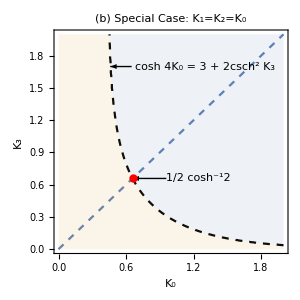

```mathematica
(*Clear["Global`*"];*)
cleanRegionPlot[cp_Graphics]:=Module[{points,groups,regions,lines},groups=Cases[cp,{style__,g_GraphicsGroup}:>{{style},g},Infinity];
points=First@Cases[cp,GraphicsComplex[pts_,___]:>pts,Infinity];
regions=Table[Module[{group,style,polys,edges,cover,graph},{style,group}=g;
polys=Join@@Cases[group,Polygon[pt_,___]:>pt,Infinity];
edges=Join@@(Partition[#,2,1,1]&/@polys);
cover=Cases[Tally[Sort/@edges],{e_,1}:>e];
graph=Graph[UndirectedEdge@@@cover];
{Sequence@@style,FilledCurve[List/@Line/@First/@Map[First,FindEulerianCycle/@(Subgraph[graph,#]&)/@ConnectedComponents[graph],{3}]]}],{g,groups}];
lines=Cases[cp,{__,_Line},Infinity];(*only change*)Graphics[GraphicsComplex[points,{regions,lines}],Sequence@@Options[cp]]];

{K0★,K3★}=1/2Log@*Coth/@{K0,K3};
K0◼=ArcCosh[Cosh[2K0★]^2+Sinh[2K0★]^2 Cosh[2K3]]/2;
epilogPoint[x0_,y0_,x1_,y1_,text_]:={Arrow[{{x0+x1,y0+y1},{x0,y0}}],Text[text,{x0+x1,y0+y1},{-1,0}],Red,PointSize[0.02],Point[{x0,y0}]};
phaseTransitionK1K2=Show[ContourPlot[{K3==K0,Cosh[4 K0]==3+2 Csch[K3]^2},{K0,0,2},{K3,0,2},PlotLabel->"(b) Special Case: K_1=K_2=K_0",PlotRangePadding->None,ContourStyle->{Dashed,{Dashed,Black}},ContourLabels->None,FrameLabel->{"K_0","K_3"},Epilog->{epilogPoint[ArcCosh[2]/2,ArcCosh[2]/2,0.3,0,"1/2 cosh^-12"],Arrow[{{0.65,1.7},{0.46,1.7}}],Text["cosh 4K_0 = 3 + 2csch^2 K_3",{0.68,1.7},{-1,0}]},LabelStyle->{12,FontFamily->Times,Black},ImageSize->300],
cleanRegionPlot@RegionPlot[{Callout[Cosh[4 K0]>3+2 Csch[K3]^2,"Ferromagnetic Phase",{1.3,1.9}],Callout[Cosh[4 K0]<3+2 Csch[K3]^2,"Paramagnetic Phase",{0.6,0.2}]},{K0,0,2},{K3,0,2},ImageSize->300,BoundaryStyle->None,PlotStyle->Opacity[0.1]]]
```

### K_1=K_2=K_3

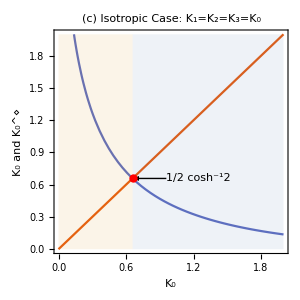

{K0→0.658479}

```mathematica
(*Clear["Global`*"];*)K0★=1/2Log@Coth@K0;K0◼=ArcCosh[Cosh[2K0★]^2+Sinh[2K0★] Cosh[2K0★]]/2;
epilogPoint[x0_,y0_,x1_,y1_,text_]:={Arrow[{{x0+x1,y0+y1},{x0,y0}}],Text[text,{x0+x1,y0+y1},{-1,0}],Red,PointSize[0.02],Point[{x0,y0}]};
phaseTransitionK1K2K3=Show[Plot[{K0,K0◼},{K0,0.,2},PlotRange->{{0,2},{0,2}},PlotLabel->"(c) Isotropic Case: K_1=K_2=K_3=K_0",PlotTheme->"Scientific",FrameLabel->{"K_0","K_0 and K_0^⋄"},GridLines->{{Log[2+√3]/2},None},GridLinesStyle->Dashed,Epilog->epilogPoint[ArcCosh[2]/2,ArcCosh[2]/2,0.3,0,"1/2 cosh^-12"],AspectRatio->1,LabelStyle->{12,FontFamily->Times,Black},ImageSize->300],
cleanRegionPlot@RegionPlot[{Callout[x>Log[2+√3]/2,"Ferromagnetic Phase",{1.3,1.9}],Callout[x<Log[2+√3]/2,"Paramagnetic Phase",{0.3,0.65}]},{x,0,2},{y,0,2},ImageSize->300,BoundaryStyle->None,PlotStyle->Opacity[0.1]]]
FindRoot[K0==K0◼,{K0,0.5}]
```

```mathematica
Overlay[{phaseTransitionGeneral,Framed[Row[{phaseTransitionK1K2,phaseTransitionK1K2K3}],FrameStyle->Transparent,ImageSize->{610,720},Alignment->{Right,Bottom}]}]
```

-Graphics3D--Graphics--Graphics-

## Thermodynamic Limit

### Periodic Boundary Condition

```mathematica
Clear["Global`*"];
(*Paramagnetic Phase K0<0.658, Ferromagnetic Phase K0>0.658*)
ℬ=Cosh[2 K0]Cosh[2 K0◼]-Sin[(k π)/(2n)]^2;𝒞=Cosh[2 K0]^2+Cosh[2 K0◼]^2-2 Cos[(k π)/(2n)]^2+1;
K0★=1/2Log@Coth@K0;K0◼=ArcCosh[Cosh[2K0★]^2+Sinh[2K0★]^2 Cosh[2K0]]/2;
ϵ[k0_]:=Block[{k=k0},ArcCosh@{ℬ+Cos[(k π)/(2n)] √(Sinh[2K0]^2 Sinh[2K0◼]^2-Sin[(k π)/(2n)]^2),ℬ-Cos[(k π)/(2n)] √(Sinh[2K0]^2 Sinh[2K0◼]^2-Sin[(k π)/(2n)]^2)}];
gap1to2[n0_]:=Block[{n=n0},
If[K0<1/2 ArcCosh[2],
1/2Total[ϵ[#]-ϵ[#-1]&/@Range[1,2n-1,2],2]+2K0◼-2K0,
1/2Total[ϵ[#]-ϵ[#-1]&/@Range[1,2n-1,2],2]]]
paraData=Block[{K0=0.6},{#,gap1to2@#}&/@Range[2,30]];
ferrData=Block[{K0=0.8},{#,gap1to2@#}&/@Range[2,30]];
```

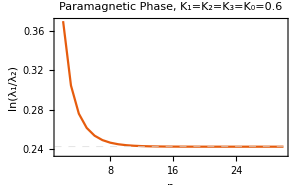
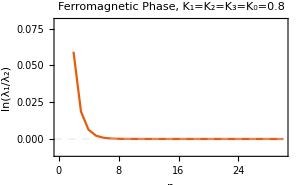

```mathematica
Row[{K0=0.6;
ListPlot[paraData,PlotRange->All,PlotTheme->"Scientific",PlotLabel->"Paramagnetic Phase, K_1=K_2=K_3=K_0="<>ToString[K0],GridLines->{None,{Min@ϵ[0]}},GridLinesStyle->Directive[Thick,Dashed],FrameLabel->{"n","ln(λ_1/λ_2)"},Joined->True,ImageSize->300,LabelStyle->{12,FontFamily->"Times",Black}],
K0=0.8;
ListPlot[ferrData,PlotTheme->"Scientific",PlotLabel->"Ferromagnetic Phase, K_1=K_2=K_3=K_0="<>ToString[K0],GridLines->{None,{0}},GridLinesStyle->Directive[Thick,Dashed],FrameLabel->{"n","ln(λ_1/λ_2)"},Joined->True,PlotRange->{-0.01,0.08},ImageSize->300,LabelStyle->{12,FontFamily->"Times",Black}]}]
```

### Open Boundary Condition

```mathematica
Clear["Global`*"];
selectθ[list_]:=SortBy[Re][Union[list,SameTest->(Abs[#1+#2]<10^-4&)]/.x_/;Re[x]<0:>-x];
ω[θ_,μ_,ν_]:=RotationMatrix[θ,UnitVector[4n,#]&/@{μ,ν}];
{K1★,K2★,K3★}=1/2Log@*Coth/@{K1,K2,K3};
ℬ=Cosh[2K1★]Cosh[2K2★]Cosh[2K3]+Sinh[2K1★] Sinh[2 K2★]+(Sinh[2 K1★]+Sinh[2 K2★])^2 Sinh[2 K3]^2/4;𝒞=(1+Cosh[4 K1★]Cosh[4 K2★]+Sinh[4 K1★] Sinh[4 K2★]Cosh[2 K3])/2+(3+Cosh[4 K1★] Cosh[4 K2★]-4Sinh[2 K1★] Sinh[2 K2★])Sinh[2 K3]^2/4;
GapOBC[n0_]:=Block[{n=n0},
Ω1=Dot@@Table[ω[-2ⅈ K1★,2j-1,2j],{j,1,2n-1,2}].Dot@@Table[ω[-2ⅈ K2★,2j-1,2j],{j,2,2n,2}];
Ω2=Dot@@Table[ω[-2ⅈ K3,2j,2j+1],{j,2,2n-1,2}];Ω3=Dot@@Table[ω[-2ⅈ K2★,2j-1,2j],{j,1,2n-1,2}].Dot@@Table[ω[-2ⅈ K1★,2j-1,2j],{j,2,2n,2}];
Ω4=Dot@@Table[ω[-2ⅈ K3,2j,2j+1],{j,1,2n-1,2}];Ω0=Ω1.Ω2.Ω3.Ω4;
θList=Chop[selectθ@Log@Eigenvalues[Ω0],10^-5];Return@Min@θList]
{K1,K2,K3}={0.6,0.6,0.6};
GapPBC=ArcCosh[ℬ-√(ℬ^2-𝒞)];
paraData=ParallelMap[{#,GapOBC[#]}&,Range[30]];
{K1,K2,K3}={0.8,0.8,0.8};
ferrData=ParallelMap[{#,GapOBC[#]}&,Range[30]];
```

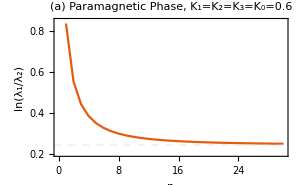
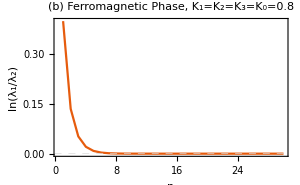

```mathematica
Row[{ListPlot[paraData,PlotTheme->"Scientific",PlotRange->{0.2,0.85},GridLines->{None,{GapPBC}},GridLinesStyle->Directive[Thick,Dashed],FrameLabel->{"n","ln(λ_1/λ_2)"},PlotLabel->"(a) Paramagnetic Phase, K_1=K_2=K_3=K_0=0.6",Joined->True,ImageSize->300,LabelStyle->{12,FontFamily->"Times",Black}],ListPlot[ferrData,PlotTheme->"Scientific",PlotRange->All,GridLines->{None,{0}},GridLinesStyle->Directive[Thick,Dashed],FrameLabel->{"n","ln(λ_1/λ_2)"},PlotLabel->"(b) Ferromagnetic Phase, K_1=K_2=K_3=K_0=0.8",Joined->True,ImageSize->300,LabelStyle->{12,FontFamily->"Times",Black}]}]
```